# Simulating experiments for NOON states

Serge Deside, Tobias Haas and Nicolas J. Cerf

Centre for Quantum Information and Communication, École polytechnique de Bruxelles, CP 165, Université libre de Bruxelles, 1050 Brussels, Belgium

We simulate experiments measuring the optimal p_3-PPT criterion for (lossy) NOON states.

Information and Instructions

The notebook is auto-run

Edit ‘Definitions and Options’ if necessary, then run the whole notebook

```mathematica
(* Evaluate here to run the notebook. *)
```

Definitions and Options

### Precision

```mathematica
(* Set precision used for plots. Higher precision (approx. 100) needed for high-quality figures, but this comes at the expense of computing time. *)
InternalPlotPoints=100;
```

### Saving/Loading

```mathematica
(* Set directory. *)
SetDirectory[NotebookDirectory[]];
```

### Global assumptions

```mathematica
(* Set global assumptions. *)
$Assumptions={0<τ<1,0<τ1<1,0<τ2<1,0<τA1<1,0<τA2<1,0<τA3<1,0<τB1<1,0<τB2<1,0<τB3<1,0<τp21<1,0<τp31<1,0<τp32<1,0<α<1,0<α1<1,0<α2<1,0<α3<1,Element[α11,Integers],α11≥0,Element[α12,Integers],α12≥0,Element[α13,Integers],α13≥0,Element[α21,Integers],α21≥0,Element[α22,Integers],α22≥0,Element[α23,Integers],α23≥0,Element[α31,Integers],α31≥0,Element[α32,Integers],α32≥0,Element[α33,Integers],α33≥0,Element[β11,Integers],β11≥0,Element[β12,Integers],β12≥0,Element[β13,Integers],β13≥0,Element[β21,Integers],β21≥0,Element[β22,Integers],β22≥0,Element[β23,Integers],β23≥0,Element[β31,Integers],β31≥0,Element[β32,Integers],β32≥0,Element[β33,Integers],β33≥0,Element[α11p,Integers],α11p≥0,Element[α12p,Integers],α12p≥0,Element[α13p,Integers],α13p≥0,Element[α21p,Integers],α21p≥0,Element[α22p,Integers],α22p≥0,Element[α23p,Integers],α23p≥0,Element[α31p,Integers],α31p≥0,Element[α32p,Integers],α32p≥0,Element[α33p,Integers],α33p≥0,Element[β11p,Integers],β11p≥0,Element[β12p,Integers],β12p≥0,Element[β13p,Integers],β13p≥0,Element[β21p,Integers],β21p≥0,Element[β22p,Integers],β22p≥0,Element[β23p,Integers],β23p≥0,Element[β31p,Integers],β31p≥0,Element[β32p,Integers],β32p≥0,Element[β33p,Integers],β33p≥0,Element[na1,Integers],na1≥0,Element[nb1,Integers],nb1≥0,Element[na2,Integers],na2≥0,Element[nb2,Integers],nb2≥0,Element[na3,Integers],na3≥0,Element[nb3,Integers],nb3≥0};
```

### Plotting

```mathematica
(* Define standard colors for figures. *)
PlotColors={RGBColor[0.206756,0.371758,0.553117,1.],RGBColor[0.120565,0.596422,0.543611,1.],RGBColor[0.404001,0.800275,0.362552,1.],RGBColor[0.8784313725490196,0.403921568627451,0.4549019607843137,1],RGBColor[101/128,5/8,113/256,1]};

(* The same with opacity. *)
PlotColorsOpacity={RGBColor[0.206756,0.371758,0.553117,0.3],RGBColor[0.120565,0.596422,0.543611,0.3],RGBColor[0.404001,0.800275,0.362552,0.3],RGBColor[0.8784313725490196,0.403921568627451,0.4549019607843137,0.3],RGBColor[101/128,5/8,113/256,0.3]};

(* Define continuous colors. *)
ContinuousColors=ColorData[{"BlueGreenYellow",{10,1}}];
ContinuousColors2=ColorData[{"BlueGreenYellow",{0.6,0}}];

(* Define nice plotmarkers for ListPlot[...]. *)
NicePlotmarkers[size_,edgethickness_,backgroundcolor_,edgecolor_,form_]:={Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Disk[{0,0},1]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Polygon[{{0,0},{1/2,-1/2},{1,0},{1/2,1/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Rectangle[{-1/2,-1/2},{1/2,1/2}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,-Sqrt[3]/2}}]},ImageSize->size]}[[form]];
```

Setup

### Density matrix

```mathematica
(* Define density matrix of the lossy NOON state in the Fock basis. *)
ρ[i_,j_,k_,l_,n_,α_,τA_,τB_]:=α^2Sum[Binomial[n,k2]τA^(n-k2)(1-τA)^k2 KroneckerDelta[i,n-k2]KroneckerDelta[j,0]KroneckerDelta[k,n-k2]KroneckerDelta[l,0],{k2,0,n}]+Sqrt[τA τB]^n α Sqrt[1-α^2] (KroneckerDelta[i,n]KroneckerDelta[j,0]KroneckerDelta[k,0]KroneckerDelta[l,n]+KroneckerDelta[i,0]KroneckerDelta[j,n]KroneckerDelta[k,n]KroneckerDelta[l,0])+(1-α^2)Sum[Binomial[n,k2]τB^(n-k2)(1-τB)^k2 KroneckerDelta[i,0]KroneckerDelta[j,n-k2]KroneckerDelta[k,0]KroneckerDelta[l,n-k2],{k2,0,n}];
```

### Analytic criteria

#### PT-moments

```mathematica
(* Define analytic expressions for the PT-moments assuming imperfect copies. *)
p2Analytic[n_,α1_,α2_,τA1_,τB1_,τA2_,τB2_]:=α1^2α2^2Sum[Binomial[n,k]^2(τA1 τA2)^(n-k)((1-τA1)(1-τA2))^k,{k,0,n}]+α1^2(1-α2^2)(1-τA1)^n (1-τB2)^n+2α1 Sqrt[1-α1^2]α2 Sqrt[1-α2^2]Sqrt[τA1 τB1 τA2 τB2]^n+(1-α1^2)α2^2(1-τB1)^n(1-τA2)^n+(1-α1^2)(1-α2^2) Sum[Binomial[n,k]^2(τB1 τB2)^(n-k)((1-τB1)(1-τB2))^k,{k,0,n}];

p3Analytic[n_,α1_,α2_,α3_,τA1_,τB1_,τA2_,τB2_,τA3_,τB3_]:=α1^2α2^2α3^2Sum[Binomial[n,k]^3(τA1 τA2 τA3)^(n-k)((1-τA1)(1-τA2)(1-τA3))^k,{k,0,n}]+α1^2α2^2(1-α3^2)((1-τA1)(1-τA2)(1-τB3))^n+α1^2(1-α2^2)α3^2((1-τA1)(1-τB2)(1-τA3))^n+α1^2(1-α2^2)(1-α3^2)((1-τA1)(1-τB2)(1-τB3))^n+(1-α1^2)α2^2α3^2((1-τB1)(1-τA2)(1-τA3))^n+(1-α1^2)α2^2(1-α3^2)((1-τB1)(1-τA2)(1-τB3))^n+(1-α1^2)(1-α2^2)α3^2((1-τB1)(1-τB2)(1-τA3))^n+(1-α1^2)(1-α2^2)(1-α3^2)Sum[Binomial[n,k]^3(τB1 τB2 τB3)^(n-k)((1-τB1)(1-τB2)(1-τB3))^k,{k,0,n}]+α1^2α2 Sqrt[1-α2^2]α3 Sqrt[1-α3^2](1-τA1)^n Sqrt[τA2 τB2 τA3 τB3]^n+(1-α1^2)α2 Sqrt[1-α2^2]α3 Sqrt[1-α3^2](1-τB1)^n Sqrt[τA2 τB2 τA3 τB3]^n+α1 Sqrt[1-α1^2]α2 ^2α3 Sqrt[1-α3^2](1-τA2)^n Sqrt[τA1 τB1 τA3 τB3]^n+α1 Sqrt[1-α1^2](1-α2^2)α3 Sqrt[1-α3^2](1-τB2)^n Sqrt[τA1 τB1 τA3 τB3]^n+α1 Sqrt[1-α1^2]α2 Sqrt[1-α2^2]α3 ^2(1-τA3)^n Sqrt[τA1 τB1 τA2 τB2]^n+α1 Sqrt[1-α1^2]α2 Sqrt[1-α2^2](1-α3 ^2)(1-τB3)^n Sqrt[τA1 τB1 τA2 τB2]^n;
```

```mathematica
(* Also, define simplified expressions for perfect copies and equal losses. *)
p2AnalyticSimple[n_,α_,τ_]:=p2Analytic[n,α,α,τ,τ,τ,τ];

p3AnalyticSimple[n_,α_,τ_]:=p3Analytic[n,α,α,α,τ,τ,τ,τ,τ,τ];
```

#### Criteria

```mathematica
(* Define analytic entanglement criteria. We assume equal losses in A and B. *)

(* Linear. *)
p3PPTLinearAnalytic[n_,αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_]:=p3Analytic[n,αp31,αp32,αp33,τp31,τp31,τp32,τp32,τp33,τp33]-(3*p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]-1)/2;

(* Quadratic. *)
p3PPTQuadraticAnalytic[n_,αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_]:=p3Analytic[n,αp31,αp32,αp33,τp31,τp31,τp32,τp32,τp33,τp33]-p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]^2;

(* Optimal. Helper functions first. *)
αNOON[n_,αp21_,αp22_,τp21_,τp22_]:=Floor[1/p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]];
xNOON[n_,αp21_,αp22_,τp21_,τp22_]:=(αNOON[n,αp21,αp22,τp21,τp22]+Sqrt[αNOON[n,αp21,αp22,τp21,τp22]*(p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]*(αNOON[n,αp21,αp22,τp21,τp22]+1)-1)])/(αNOON[n,αp21,αp22,τp21,τp22]*(αNOON[n,αp21,αp22,τp21,τp22]+1))//Simplify;

p3PPTOptimalAnalytic[n_,αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_]:=p3Analytic[n,αp31,αp32,αp33,τp31,τp31,τp32,τp32,τp33,τp33]-αNOON[n,αp21,αp22,τp21,τp22]*(xNOON[n,αp21,αp22,τp21,τp22]^3)-(1-αNOON[n,αp21,αp22,τp21,τp22]*xNOON[n,αp21,αp22,τp21,τp22])^3//Simplify;
```

```mathematica
(* The same for the simplified expressions. *)

(* Linear. *)
p3PPTLinearAnalyticSimple[n_,α_,τ_]:=p3AnalyticSimple[n,α,τ]-(3*p2AnalyticSimple[n,α,τ]-1)/2;

(* Quadratic. *)
p3PPTQuadraticAnalyticSimple[n_,α_,τ_]:=p3AnalyticSimple[n,α,τ]-p2AnalyticSimple[n,α,τ]^2;

(* Optimal. Helper functions first. *)
αNOONSimple[n_,α_,τ_]:=Floor[1/p2AnalyticSimple[n,α,τ]];
xNOONSimple[n_,α_,τ_]:=(αNOONSimple[n,α,τ]+Sqrt[αNOONSimple[n,α,τ]*(p2AnalyticSimple[n,α,τ]*(αNOONSimple[n,α,τ]+1)-1)])/(αNOONSimple[n,α,τ]*(αNOONSimple[n,α,τ]+1))//Simplify;

p3PPTOptimalAnalyticSimple[n_,α_,τ_]:=p3AnalyticSimple[n,α,τ]-αNOONSimple[n,α,τ]*(xNOONSimple[n,α,τ]^3)-(1-αNOONSimple[n,α,τ]*xNOONSimple[n,α,τ])^3//Simplify;
```

#### Error models (to do)

```mathematica
(* Define the mean and its standard deviation of some criterion for finite sample size. *)

(* Linear. *)
p3PPTLinearAnalyticError[samples_,n_,αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_]:=Sqrt[((1-p3Analytic[n,αp31,αp32,αp33,τp31,τp31,τp32,τp32,τp33,τp33]^2)+(9/4)(1-p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]))/samples];

(* Quadratic. *)
p3PPTQuadraticAnalyticError[samples_,n_,αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_]:=Sqrt[-1/samples(-1+1/(-1+samples)2 (-1+p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]^2) (1+(-3+2 samples) p2Analytic[n,αp21,αp22,τp21,τp21,τp22,τp22]^2)+p3Analytic[n,αp31,αp32,αp33,τp31,τp31,τp32,τp32,τp33,τp33]^2)];

(* Optimal. *)
```

```mathematica
(* The same for the simplified expressions. *)

(* Linear. *)
p3PPTLinearAnalyticErrorSimple[samples_,n_,α_,τ_]:=Sqrt[((1-p3AnalyticSimple[n,α,τ]^2)+(9/4)(1-p2AnalyticSimple[n,α,τ]^2) )/samples];

(* Quadratic. *)
p3PPTQuadraticAnalyticErrorSimple[samples_,n_,α_,τ_]:=Sqrt[-(-1+(2 (-1+p2AnalyticSimple[n,α,τ]^2) (1+(-3+2 samples) p2AnalyticSimple[n,α,τ]^2))/(-1+samples)+p3AnalyticSimple[n,α,τ]^2)/samples];

(* Optimal. *)
```

### Photon-number distributions

#### Circuit for purity p_2

```mathematica
(* Define photon-number output distribution of the optical circuit for Subscript[p, 2]. We assume equal losses in subsystems A and B. *)
PhotonNumbersp2Definition[na2_,nb2_,n_,α1_,α2_,τ1_,τ2_]:=Sum[(1/(Factorial[na1]Factorial[nb1]Factorial[na2]Factorial[nb2]))(1/(2^(na1+nb1+na2+nb2)))Sum[(-1)^(α2pp+β2+α2p+β2p) Binomial[na1,α1pp]Binomial[na2,α2pp]Binomial[na1,α1p]Binomial[na2,α2p]Binomial[nb1,β1]Binomial[nb2,β2]Binomial[nb1,β1p]Binomial[nb2,β2p]Sqrt[Factorial[na1-α1pp+na2-α2pp]Factorial[α1pp+α2pp]Factorial[na1-α1p+na2-α2p]Factorial[α1p+α2p]Factorial[nb1-β1+nb2-β2]Factorial[β1+β2]Factorial[nb1-β1p+nb2-β2p]Factorial[β1p+β2p]]ρ[na1-α1pp+na2-α2pp,nb1-β1+nb2-β2,na1-α1p+na2-α2p,nb1-β1p+nb2-β2p,n,α1,τ1,τ1]ρ[α1pp+α2pp,β1+β2,α1p+α2p,β1p+β2p,n,α2,τ2,τ2],{α1pp,0,na1},{β1,0,nb1},{α1p,0,na1},{β1p,0,nb1},{α2pp,0,na2},{β2,0,nb2},{α2p,0,na2},{β2p,0,nb2}],{na1,0,2n},{nb1,0,2n}];
```

```mathematica
(* Compute it for N=1. *)
PhotonNumbersp2N1Data=Flatten[ParallelTable[{na2,nb2,PhotonNumbersp2Definition[na2,nb2,1,α1,α2,τ1,τ2]},{na2,0,2},{nb2,0,2}],1]//FullSimplify
```

```mathematica
(* The latter's result is defined here. *)
PhotonNumbersp2N1Data={{0,0,1/4 (4-2 τ2+τ1 (-2+(2-α2^2+2 α1 α2 √((-1+α1^2) (-1+α2^2))+α1^2 (-1+2 α2^2)) τ2))},{0,1,1/4 (-2 (-1+α2^2) τ2+τ1 (2-4 τ2+3 α2^2 τ2-2 α1 α2 √((-1+α1^2) (-1+α2^2)) τ2+α1^2 (-2+3 τ2-2 α2^2 τ2)))},{0,2,1/2 (-1+α1^2) (-1+α2^2) τ1 τ2},{1,0,1/4 (-α2^2 (-2+τ1) τ2-2 α1 α2 √((-1+α1^2) (-1+α2^2)) τ1 τ2-α1^2 τ1 (-2+τ2+2 α2^2 τ2))},{1,1,1/4 (α2^2+α1 (α1-2 α1 α2^2+2 α2 √((-1+α1^2) (-1+α2^2)))) τ1 τ2},{1,2,0},{2,0,1/2 α1^2 α2^2 τ1 τ2},{2,1,0},{2,2,0}};
```

```mathematica
(* And define piecewise function based on the latter. *)
PhotonNumbersp2N1[na2_,nb2_,α1_,α2_,τ1_,τ2_]=Piecewise[Table[{PhotonNumbersp2N1Data[[i,3]],PhotonNumbersp2N1Data[[i,1]]-0.5≤na2≤PhotonNumbersp2N1Data[[i,1]]+0.5&&PhotonNumbersp2N1Data[[i,2]]-0.5≤nb2≤PhotonNumbersp2N1Data[[i,2]]+0.5},{i,1,Length[PhotonNumbersp2N1Data]}]];
```

#### Circuit for third PT-moment p_3 for N=1

```mathematica
(* Define photon-number output distribution of the optical circuit for Subscript[p, 3]. We again assume equal losses in subsystems A and B, but also set N=1. *) 

(* Define helper function first. *)
PhotonNumbersp3Helper[na2_,nb2_,na3_,nb3_,α1_,α2_,α3_,τ1_,τ2_,τ3_]:=Sum[(1/(Factorial[na1]Factorial[nb1]))*(1/(3^(na1+nb1)))*Multinomial[α11,α12,na1-(α11+α12)]*Multinomial[β11,β12,nb1-(β11+β12)]*Multinomial[α11p,α12p,na1-(α11p+α12p)]*Multinomial[β11p,β12p,nb1-(β11p+β12p)]*Sqrt[Factorial[α11+α21+α31]Factorial[α12+α22+α32]Factorial[na1-(α11+α12)+na2-(α21+α22)+na3-(α31+α32)]Factorial[β11+β21+β31]Factorial[β12+β22+β32]Factorial[nb1-(β11+β12)+nb2-(β21+β22)+nb3-(β31+β32)]Factorial[α11p+α21p+α31p]Factorial[α12p+α22p+α32p]Factorial[na1-(α11p+α12p)+na2-(α21p+α22p)+na3-(α31p+α32p)]Factorial[β11p+β21p+β31p]Factorial[β12p+β22p+β32p]Factorial[nb1-(β11p+β12p)+nb2-(β21p+β22p)+nb3-(β31p+β32p)]]ρ[α11+α21+α31,β11+β21+β31,α11p+α21p+α31p,β11p+β21p+β31p,1,α1,τ1,τ1]*ρ[α12+α22+α32,β12+β22+β32,α12p+α22p+α32p,β12p+β22p+β32p,1,α2,τ2,τ2]*ρ[na1-(α11+α12)+na2-(α21+α22)+na3-(α31+α32),nb1-(β11+β12)+nb2-(β21+β22)+nb3-(β31+β32),na1-(α11p+α12p)+na2-(α21p+α22p)+na3-(α31p+α32p),nb1-(β11p+β12p)+nb2-(β21p+β22p)+nb3-(β31p+β32p),1,α3,τ3,τ3],{na1,0,3},{nb1,0,3},{α11,0,na1},{α12,0,na1-α11},{β11,0,nb1},{β12,0,nb1-β11},{α11p,0,na1},{α12p,0,na1-α11p},{β11p,0,nb1},{β12p,0,nb1-β11p}];
```

```mathematica
(* Now the output distribution itself. *)
PhotonNumbersp3Definition[na2_,nb2_,na3_,nb3_,α1_,α2_,α3_,τ1_,τ2_,τ3_]:=(1/(Factorial[na2]Factorial[nb2]Factorial[na3]Factorial[nb3]))*(1/(3^(na2+nb2+na3+nb3)))Sum[PhotonNumbersp3Helper[na2,nb2,na3,nb3,α1,α2,α3,τ1,τ2,τ3]*Multinomial[α21,α22,na2-(α21+α22)]Multinomial[α31,α32,na3-(α31+α32)]Multinomial[β21,β22,nb2-(β21+β22)]Multinomial[β31,β32,nb3-(β31+β32)]Multinomial[α21p,α22p,na2-(α21p+α22p)]Multinomial[α31p,α32p,na3-(α31p+α32p)]Multinomial[β21p,β22p,nb2-(β21p+β22p)]Multinomial[β31p,β32p,nb3-(β31p+β32p)]*Cos[(2π/3)*(3 na2+3 na3+3 nb2+3 nb3-2 α21-α21p-α22+α22p-α31-2 α31p+α32-α32p-2 β21-β21p-β22+β22p-β31-2 β31p+β32-β32p)],{α21,0,na2},{α22,0,na2-α21},{α31,0,na3},{α32,0,na3-α31},{β21,0,nb2},{β22,0,nb2-β21},{β31,0,nb3},{β32,0,nb3-β31},{α21p,0,na2},{α22p,0,na2-α21p},{α31p,0,na3},{α32p,0,na3-α31p},{β21p,0,nb2},{β22p,0,nb2-β21p},{β31p,0,nb3},{β32p,0,nb3-β31p}];
```

```mathematica
(* Compute it for N=1. This takes around 90min and is thus omitted by default. *)
PhotonNumbersp3N1Data=Flatten[ParallelTable[{na2,nb2,na3,nb3,PhotonNumbersp3Definition[na2,nb2,na3,nb3,α1,α2,α3,τ1,τ2,τ3]},{na2,0,3},{nb2,0,3-na2},{na3,0,3-na2-nb2},{nb3,0,3-na2-nb2-na3}],3]//FullSimplify//AbsoluteTiming
```

```mathematica
(* The latter's result is defined here. *)
PhotonNumbersp3N1Data={{0,0,0,0,1/27 (3 (9-6 τ3+τ2 (-6+(5-α2^2+(-1+2 α2^2) α3^2) τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))-τ1 (3 (6+(-5+α3^2+α1^2 (1-2 α3^2)) τ3-2 α1 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+τ2 (-15-2 (-6+α3^2) τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3+2 (-1+α3^2) τ3)+α1^2 (3+2 α2^2 (-3+τ3)+2 (-1+α3^2) τ3)+2 α1 (α2 √((-1+α1^2) (-1+α2^2)) (-3+τ3)+α3 √((-1+α1^2) (-1+α3^2) τ3^2)))))},{0,0,0,1,1/27 (-9 (-1+α3^2) τ3-3 τ2 (-3+5 τ3-3 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3+(-3+α3^2) τ3))-τ1 (-9+15 τ3-9 α3^2 τ3+τ2 (15-18 τ3+8 α3^2 τ3-2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (-9+8 τ3-3 α3^2 τ3))+α1 (α3 (3-2 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 τ2 √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (3+(-2+α3^2) τ3))+α1^2 (9+3 (-3+α3^2) τ3+τ2 (-9+8 τ3-3 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+3 α2^2 (1+(-1+α3^2) τ3)))))},{0,0,0,2,2/27 (3 (-1+α1^2) (-1+α3^2) τ1 τ3+3 (-1+α2^2) (-1+α3^2) τ2 τ3+τ1 τ2 (3-9 τ3+7 α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (-3+7 τ3-5 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (-3+7 τ3-5 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3-5 τ3+3 α3^2 τ3))))},{0,0,0,3,-2/9 (-1+α1^2) (-1+α2^2) (-1+α3^2) τ1 τ2 τ3},{0,0,1,0,1/27 (α3^2 (9-6 τ1-6 τ2+5 τ1 τ2) τ3+α2 α3 (-3+τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (9-3 (2+α3^2) τ3+τ1 (-6+5 τ3))+α1 τ1 (α3 (-3+τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 τ2 √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (-3+τ3+α3^2 τ3))+α1^2 τ1 (9-3 (2+α3^2) τ3+τ2 (-6+5 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+3 α2^2 (-1+α3^2 τ3))))},{0,0,1,1,1/27 (α3^2 (3 τ1+3 τ2-5 τ1 τ2) τ3+α2 α3 (6-7 τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (3 τ1+(3-5 τ1+α3^2 (-6+5 τ1)) τ3)+α1^2 τ1 ((3-6 α2^2) τ2+(3+5 (-1+α2^2) τ2+α3^2 (-6+5 τ2)) τ3)+α1 τ1 (α2 √((-1+α1^2) (-1+α2^2)) τ2 (6-7 τ3)+α3 (6-7 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)))},{0,0,1,2,2/27 τ1 τ2 (α3^2 τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)-2 α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α3^2 τ3+α2^2 (-2+3 α3^2) τ3-2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{0,0,2,0,-2/27 (α2^2 α3^2 (-3+2 τ1) τ2 τ3+α1 α2 α3 τ1 τ2 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 τ1 (α3^2 (-3+2 τ2) τ3+α2 α3 τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (-3+2 τ3+3 α3^2 τ3)))},{0,0,2,1,2/27 τ1 τ2 (α2^2 α3^2 τ3+2 α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (α3^2 τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-3 α3^2 τ3)))},{0,0,3,0,2/9 α1^2 α2^2 α3^2 τ1 τ2 τ3},{0,1,0,0,1/27 (-9 (-1+α3^2) τ3-3 τ2 (-3+5 τ3-3 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3+(-3+α3^2) τ3))-τ1 (-9+15 τ3-9 α3^2 τ3+τ2 (15-18 τ3+8 α3^2 τ3-2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (-9+8 τ3-3 α3^2 τ3))+α1 (α3 (3-2 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 τ2 √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (3+(-2+α3^2) τ3))+α1^2 (9+3 (-3+α3^2) τ3+τ2 (-9+8 τ3-3 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+3 α2^2 (1+(-1+α3^2) τ3)))))},{0,1,0,1,1/27 (3 (-1+α1^2) (-1+α3^2) τ1 τ3+3 (-1+α2^2) (-1+α3^2) τ2 τ3+τ1 τ2 (3-2 α3^2 τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (-3+(-2+4 α3^2) τ3)-2 α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (-3+(-2+4 α3^2) τ3-2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3+(4-6 α3^2) τ3))))},{0,1,0,2,0},{0,1,1,0,1/27 (α3^2 (3 τ1+3 τ2-5 τ1 τ2) τ3+α2 α3 (-3+5 τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (3 τ1+(3-5 τ1+α3^2 (-6+5 τ1)) τ3)+α1^2 τ1 ((3-6 α2^2) τ2+(3+5 (-1+α2^2) τ2+α3^2 (-6+5 τ2)) τ3)+α1 τ1 (α3 (-3+5 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (-3+5 τ3)))},{0,1,1,1,1/27 τ1 τ2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α2^2 τ3+(-2+3 α2^2) α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{0,1,2,0,-2/27 τ1 τ2 (-α2^2 α3^2 τ3+α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (-α3^2 τ3+α2^2 (-1+3 α3^2) τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{0,2,0,0,2/27 (3 (-1+α1^2) (-1+α3^2) τ1 τ3+3 (-1+α2^2) (-1+α3^2) τ2 τ3+τ1 τ2 (3-9 τ3+7 α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (-3+7 τ3-5 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (-3+7 τ3-5 α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (3-5 τ3+3 α3^2 τ3))))},{0,2,0,1,0},{0,2,1,0,2/27 τ1 τ2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α2^2 τ3+(-2+3 α2^2) α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{0,3,0,0,-2/9 (-1+α1^2) (-1+α2^2) (-1+α3^2) τ1 τ2 τ3},{1,0,0,0,1/27 (α3^2 (9-6 τ1-6 τ2+5 τ1 τ2) τ3+α2 α3 (-3+τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (9-3 (2+α3^2) τ3+τ1 (-6+5 τ3))+α1 τ1 (α3 (-3+τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 τ2 √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (-3+τ3+α3^2 τ3))+α1^2 τ1 (9-3 (2+α3^2) τ3+τ2 (-6+5 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+3 α2^2 (-1+α3^2 τ3))))},{1,0,0,1,1/27 (α3^2 (3 τ1+3 τ2-5 τ1 τ2) τ3+α2 α3 (-3+5 τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (3 τ1+(3-5 τ1+α3^2 (-6+5 τ1)) τ3)+α1^2 τ1 ((3-6 α2^2) τ2+(3+5 (-1+α2^2) τ2+α3^2 (-6+5 τ2)) τ3)+α1 τ1 (α3 (-3+5 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)+α2 √((-1+α1^2) (-1+α2^2)) τ2 (-3+5 τ3)))},{1,0,0,2,2/27 τ1 τ2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α2^2 τ3+(-2+3 α2^2) α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{1,0,1,0,1/27 (α2^2 α3^2 (3-2 τ1) τ2 τ3+2 α1 α2 α3 τ1 τ2 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 τ1 (α3^2 (3-2 τ2) τ3+2 α2 α3 τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (3-2 τ3+6 α3^2 τ3)))},{1,0,1,1,1/27 τ1 τ2 (α2^2 α3^2 τ3-α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-3 α3^2 τ3)))},{1,0,2,0,0},{1,1,0,0,1/27 (α3^2 (3 τ1+3 τ2-5 τ1 τ2) τ3+α2 α3 (6-7 τ1) τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (3 τ1+(3-5 τ1+α3^2 (-6+5 τ1)) τ3)+α1^2 τ1 ((3-6 α2^2) τ2+(3+5 (-1+α2^2) τ2+α3^2 (-6+5 τ2)) τ3)+α1 τ1 (α2 √((-1+α1^2) (-1+α2^2)) τ2 (6-7 τ3)+α3 (6-7 τ2) √((-1+α1^2) (-1+α3^2) τ3^2)))},{1,1,0,1,1/27 τ1 τ2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)+α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α2^2 τ3+(-2+3 α2^2) α3^2 τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{1,1,1,0,1/27 τ1 τ2 (α2^2 α3^2 τ3-α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (α3^2 τ3-α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-3 α3^2 τ3)))},{1,2,0,0,2/27 τ1 τ2 (α3^2 τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-2 α3^2 τ3)-2 α1 (α2 √((-1+α1^2) (-1+α2^2)) (-1+α3^2) τ3-α3 √((-1+α1^2) (-1+α3^2) τ3^2)+α2^2 α3 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (τ3-2 α3^2 τ3+α2^2 (-2+3 α3^2) τ3-2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{2,0,0,0,-2/27 (α2^2 α3^2 (-3+2 τ1) τ2 τ3+α1 α2 α3 τ1 τ2 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 τ1 (α3^2 (-3+2 τ2) τ3+α2 α3 τ2 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 τ2 (-3+2 τ3+3 α3^2 τ3)))},{2,0,0,1,-2/27 τ1 τ2 (-α2^2 α3^2 τ3+α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (-α3^2 τ3+α2^2 (-1+3 α3^2) τ3+α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)))},{2,0,1,0,0},{2,1,0,0,2/27 τ1 τ2 (α2^2 α3^2 τ3+2 α1 α2 α3 (√((-1+α1^2) (-1+α2^2)) α3 τ3+α2 √((-1+α1^2) (-1+α3^2) τ3^2))+α1^2 (α3^2 τ3+2 α2 α3 √((-1+α2^2) (-1+α3^2) τ3^2)+α2^2 (τ3-3 α3^2 τ3)))},{3,0,0,0,2/9 α1^2 α2^2 α3^2 τ1 τ2 τ3}};
```

```mathematica
(* Define piecewise function based on the latter. *)
PhotonNumbersp3N1[na2_,nb2_,na3_,nb3_,α1_,α2_,α3_,τ1_,τ2_,τ3_]=Piecewise[Table[{PhotonNumbersp3N1Data[[i,5]],PhotonNumbersp3N1Data[[i,1]]-0.5≤na2≤PhotonNumbersp3N1Data[[i,1]]+0.5&&PhotonNumbersp3N1Data[[i,2]]-0.5≤nb2≤PhotonNumbersp3N1Data[[i,2]]+0.5&&PhotonNumbersp3N1Data[[i,3]]-0.5≤na3≤PhotonNumbersp3N1Data[[i,3]]+0.5&&PhotonNumbersp3N1Data[[i,4]]-0.5≤nb3≤PhotonNumbersp3N1Data[[i,4]]+0.5},{i,1,Length[PhotonNumbersp3N1Data]}]];
```

### Sampling

#### Circuit for purity p_2

```mathematica
(* Define a function which produces a given number of samples from the photon-number distribution of the Subscript[p, 2] circuit. *)
Samplep2[αp21_,αp22_,τp21_,τp22_,start_,end_,steps_,repetitions_]:=Module[{events=PhotonNumbersp2N1Data[[All,{1,2}]],probabilities=PhotonNumbersp2N1Data[[All,3]]/.{α1->αp21,α2->αp22,τ1->τp21,τ2->τp22}},Table[Table[RandomChoice[probabilities->events,j],{i,1,repetitions,1}],{j,start,end,steps}]];
```

```mathematica
(* Define a function which computes Subscript[p, 2] based on the output of the latter. *)
p2Numerical[data_]:=ParallelTable[Module[{samples=Table[Length[data[[i,1]]],{i,1,Length[data]}]},Table[Sum[(-1)^(data[[i,j,k,1]]+data[[i,j,k,2]]),{k,1,samples[[i]]}]/samples[[i]]//N,{j,1,Length[data[[1]]],1}]],{i,1,Length[data],1}];
```

#### Circuit for third PT-moment p_3

```mathematica
(* Define a function which produces a given number of samples from the photon-number distribution of the Subscript[p, 3] circuit. *)
Samplep3[αp31_,αp32_,αp33_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{events=PhotonNumbersp3N1Data[[All,{1,2,3,4}]],probabilities=PhotonNumbersp3N1Data[[All,5]]/.{α1->αp31,α2->αp32,α3->αp33,τ1->τp31,τ2->τp32,τ3->τp33}},Table[Table[RandomChoice[probabilities->events,j],{i,1,repetitions,1}],{j,start,end,steps}]];
```

```mathematica
(* Define a function which computes Subscript[p, 3] based on the output of the latter. *)
p3Numerical[data_]:=ParallelTable[Module[{samples=Table[Length[data[[i,1]]],{i,1,Length[data]}]},Table[Sum[(-1)^((-2/3)*(data[[i,j,k,1]]+2*data[[i,j,k,2]]+2*data[[i,j,k,3]]+data[[i,j,k,4]])),{k,1,samples[[i]]}]/samples[[i]]//N,{j,1,Length[data[[1]]],1}]],{i,1,Length[data],1}];
```

```mathematica
(* Compute Subscript[p, 2] and Subscript[p, 3] for given input values. *)
p2p3Numerical[αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{p2=Samplep2[αp21,αp22,τp21,τp22,start,end,steps,repetitions],p3=Samplep3[αp31,αp32,αp33,τp31,τp32,τp33,start,end,steps,repetitions]},{p2Numerical[p2],p3Numerical[p3]}];
```

#### Criteria

```mathematica
(* Compute linear criterion for each sample size, with mean and variance obtained by averaging over all repetitions. *)
p3PPTLinearNumerical[αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3Numerical[αp21,αp22,αp31,αp32,αp33,τp21,τp22,τp31,τp32,τp33,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{witness=Table[p2p3[[2,i,j]]-(3*p2p3[[1,i,j]]-1)/2,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]];
```

```mathematica
(* Compute quadratic criterion. *)
p3PPTQuadraticNumerical[αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3Numerical[αp21,αp22,αp31,αp32,αp33,τp21,τp22,τp31,τp32,τp33,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{witness=Table[p2p3[[2,i,j]]-p2p3[[1,i,j]]^2,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]];
```

```mathematica
(* Define helper functions first. *)

(* Compute α and x appearing in the optimal criterion for given Subscript[p, 2] and Subscript[p, 3]. *)
αxNumerical[p2p3_,samplesets_,repetitions_]:=Module[{αNumeric=Table[Floor[1/p2p3[[1,i,j]]],{i,1,samplesets,1},{j,1,repetitions,1}]},{αNumeric,Table[(αNumeric[[i,j]]+Sqrt[αNumeric[[i,j]]*(p2p3[[1,i,j]]*(αNumeric[[i,j]]+1)-1)])/(αNumeric[[i,j]]*(αNumeric[[i,j]]+1)),{i,1,samplesets,1},{j,1,repetitions,1}]}];

(* Compute optimal witness. *)
p3PPTOptimalNumerical[αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3Numerical[αp21,αp22,αp31,αp32,αp33,τp21,τp22,τp31,τp32,τp33,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{αxNumeric=αxNumerical[p2p3,samplesets,repetitions]},Module[{witness=Table[p2p3[[2,i,j]]-αxNumeric[[1,i,j]]*(αxNumeric[[2,i,j]]^3)-(1-αxNumeric[[1,i,j]]*αxNumeric[[2,i,j]])^3,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]]];
```

```mathematica
(* Finally, set up function which computes all witnesses for one data set at once. *)
p3PPTAllNumerical[αp21_,αp22_,αp31_,αp32_,αp33_,τp21_,τp22_,τp31_,τp32_,τp33_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3Numerical[αp21,αp22,αp31,αp32,αp33,τp21,τp22,τp31,τp32,τp33,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{αxNumeric=αxNumerical[p2p3,samplesets,repetitions]},Module[{linearwitness=Table[p2p3[[2,i,j]]-(3*p2p3[[1,i,j]]-1)/2,{i,1,samplesets,1},{j,1,repetitions,1}],quadraticwitness=Table[p2p3[[2,i,j]]-p2p3[[1,i,j]]^2,{i,1,samplesets,1},{j,1,repetitions,1}],optimalwitness=Table[p2p3[[2,i,j]]-αxNumeric[[1,i,j]]*(αxNumeric[[2,i,j]]^3)-(1-αxNumeric[[1,i,j]]*αxNumeric[[2,i,j]])^3,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),{Around[Mean[linearwitness[[i]]]//Re,StandardDeviation[linearwitness[[i]]]]},{Around[Mean[quadraticwitness[[i]]]//Re,StandardDeviation[quadraticwitness[[i]]]]},{Around[Mean[optimalwitness[[i]]]//Re,StandardDeviation[optimalwitness[[i]]]]}},{i,1,samplesets,1}]]]];
```

### Noisy sampling

#### Helper functions

```mathematica
(* Define some helper functions to sample from distributions with fluctuating parameters. *)

(* Required nummber of samples for given set numbers. *)
NumberOfSamples[start_,end_,steps_,repetitions_]:=repetitions*Sum[i,{i,start,end,steps}];

(* Subdivision of full sample set into subsets according to repetitions, number of samples per repetition, etc. *)
ReSample[start_,end_,steps_,repetitions_]:=Flatten[Table[Table[j,{i,1,repetitions}],{j,start,end,steps}],2];

(* Sample from a normal distribution with mean x and standard deviation δx within the interval [0,1]. *)
ConstrainedSample[x_,δx_]:=Module[{sample=RandomVariate[NormalDistribution[x,δx],10]},Table[If[1≥sample[[i]]≥0,sample[[i]],Nothing],{i,1,Length[sample]}][[1]]];

(* Sample physical parameters used for Subscript[p, 2] and Subscript[p, 3] for given number of samples. *)

(* Subscript[p, 2]. *)
Samplep2Parameters[α_,δα_,τ_,δτ_,samples_]:=Table[{If[δα==0,α,ConstrainedSample[α,δα]],If[δα==0,α,ConstrainedSample[α,δα]],If[δτ==0,τ,ConstrainedSample[τ,δτ]],If[δτ==0,τ,ConstrainedSample[τ,δτ]]},{i,1,samples,1}];

(* Subscript[p, 3]. *)
Samplep3Parameters[α_,δα_,τ_,δτ_,samples_]:=Table[{If[δα==0,α,ConstrainedSample[α,δα]],If[δα==0,α,ConstrainedSample[α,δα]],If[δα==0,α,ConstrainedSample[α,δα]],If[δτ==0,τ,ConstrainedSample[τ,δτ]],If[δτ==0,τ,ConstrainedSample[τ,δτ]],If[δτ==0,τ,ConstrainedSample[τ,δτ]]},{i,1,samples,1}];
```

#### Circuit for purity p_2

```mathematica
(* Define a function which produces a given number of samples from the photon-number distribution of the Subscript[p, 2] circuit. *)
Samplep2Noisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{samples=NumberOfSamples[start,end,steps,repetitions],resample=ReSample[start,end,steps,repetitions]},Module[{parameters=Samplep2Parameters[α,δα,τ,δτ,samples]},Module[{events=PhotonNumbersp2N1Data[[All,{1,2}]],probabilities=Table[PhotonNumbersp2N1Data[[All,3]]/.{α1->parameters[[i,1]],α2->parameters[[i,2]],τ1->parameters[[i,3]],τ2->parameters[[i,4]]},{i,1,samples}]},Module[{data=Table[RandomChoice[probabilities[[i]]->events],{i,1,samples,1}]},Partition[TakeList[data,resample],repetitions]]]]];
```

#### Circuit for third PT-moment p_3

```mathematica
(* Define a function which produces a given number of samples from the photon-number distribution of the Subscript[p, 3] circuit. *)
Samplep3Noisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{samples=NumberOfSamples[start,end,steps,repetitions],resample=ReSample[start,end,steps,repetitions]},Module[{parameters=Samplep3Parameters[α,δα,τ,δτ,samples]},Module[{events=PhotonNumbersp3N1Data[[All,{1,2,3,4}]],probabilities=Table[PhotonNumbersp3N1Data[[All,5]]/.{α1->parameters[[i,1]],α2->parameters[[i,2]],α3->parameters[[i,3]],τ1->parameters[[i,4]],τ2->parameters[[i,5]],τ3->parameters[[i,6]]},{i,1,samples}]},Module[{data=Table[RandomChoice[probabilities[[i]]->events],{i,1,samples,1}]},Partition[TakeList[data,resample],repetitions]]]]];
```

```mathematica
(* Compute Subscript[p, 2] and Subscript[p, 3] for given input values. *)
p2p3NumericalNoisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{p2=Samplep2Noisy[α,δα,τ,δτ,start,end,steps,repetitions],p3=Samplep3Noisy[α,δα,τ,δτ,start,end,steps,repetitions]},{p2Numerical[p2],p3Numerical[p3]}];
```

#### Criteria

```mathematica
(* Set up linear criterion. *)
p3PPTLinearNumericalNoisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3NumericalNoisy[α,δα,τ,δτ,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{witness=Table[p2p3[[2,i,j]]-(3*p2p3[[1,i,j]]-1)/2,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]];
```

```mathematica
(* Set up quadratic criterion. *)
p3PPTQuadraticNumericalNoisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3NumericalNoisy[α,δα,τ,δτ,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{witness=Table[p2p3[[2,i,j]]-p2p3[[1,i,j]]^2,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]];
```

```mathematica
(* Optimal. *)
p3PPTOptimalNumericalNoisy[α_,δα_,τ_,δτ_,start_,end_,steps_,repetitions_]:=Module[{p2p3=p2p3NumericalNoisy[α,δα,τ,δτ,start,end,steps,repetitions],samplesets=((end-start)/steps)+1},Module[{αxNumeric=αxNumerical[p2p3,samplesets,repetitions]},Module[{witness=Table[p2p3[[2,i,j]]-αxNumeric[[1,i,j]]*(αxNumeric[[2,i,j]]^3)-(1-αxNumeric[[1,i,j]]*αxNumeric[[2,i,j]])^3,{i,1,samplesets,1},{j,1,repetitions,1}]},Table[{start+steps*(i-1),Around[Mean[witness[[i]]]//Re,StandardDeviation[witness[[i]]]]},{i,1,samplesets,1}]]]];
```

Main plots

### Losses

#### Data

```mathematica
(* Compute necessary functions first. We choose N=1,...,10. Takes some time. *)
p3PPTOptimalAnalyticLosses=Table[p3PPTOptimalAnalyticSimple[n,1/Sqrt[2],τ],{n,1,10,1}];
```

```mathematica
(* Calculate crossovers. Takes some time. Evaluate only if necessary. *)
p3PPTOptimalAnalyticLossesCrossovers=Module[{τInternal=ParallelTable[τ/.NSolve[p3PPTOptimalAnalyticLosses[[i]]==0&&0<τ<1,τ,WorkingPrecision->3][[1]],{i,1,Length[p3PPTOptimalAnalyticLosses]}]},Table[{{τInternal[[i]],0}},{i,1,Length[p3PPTOptimalAnalyticLosses]}]]
```

{{{0.5,0}},{{0.5,0}},{{0.509,0}},{{0.596,0}},{{0.657,0}},{{0.699,0}},{{0.738,0}},{{0.769,0}},{{0.79,0}},{{0.805,0}}}

```mathematica
(* Define the latter's result. *)
p3PPTOptimalAnalyticLossesCrossovers={{{0.5`3.,0}},{{0.5`3.,0}},{{0.5085677121659275363`3.,0}},{{0.5963432886751626023`3.,0}},{{0.6572407066506317952`3.,0}},{{0.6987719487206978826`3.,0}},{{0.7376034109292461678`3.,0}},{{0.7689595724435961976`3.,0}},{{0.7896700049737632321`3.,0}},{{0.8053021316211001313`3.,0}}};
```

```mathematica
(* Define τ points for N=1. *)
p3PPTOptimalAnalyticN1τPoints=Quiet@{{{0.9,p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.9]}},{{0.75,p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.75]}},{{0.6,p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.6]}}};

(* Define corresponding ListPlots. *)
SubfigureaPoints[i_,j_]:=ListPlot[p3PPTOptimalAnalyticN1τPoints[[i]],PlotStyle->{PointSize[Large],PlotColors[[j]]}];
```

```mathematica
(* Set up plot styles. *)
LossesPlotStyleInternal=Table[{ContinuousColors[i],Thickness[0.01],Opacity[0.8]},{i,1,10}];
LossesPlotMarkersInternal=Table[NicePlotmarkers[11,0.28,White,ContinuousColors[i],1],{i,1,10}];
```

#### Plot

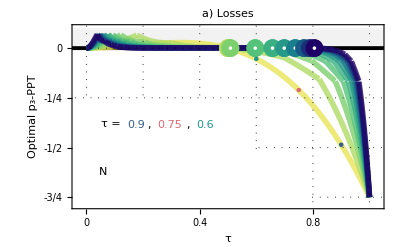

```mathematica
(* Plot the optimal PPT criterion against the loss parameter for several N. *)
p3PPTOptimalAnalyticLossesPlot=Legended[Show[Plot[0,{τ,-1,2},PlotRange->{{-0.03,1.03},{-0.79,0.1}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Thickness[0.007],Black}},Filling->{1->{0.1,Directive[Gray,Opacity[0.1]]}},FrameLabel->{Style["τ",Black,FontSize->15],Style["Optimal p_3-PPT",Black,FontSize->15]},FrameTicks->{{{{-0.75,"-3/4"},{-0.5,"-1/2"},{-0.25,"-1/4"},0},None},{{0,0.2,0.4,0.6,0.8,1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.2,0.4,0.6,0.8,1},{-0.75,-0.5,-0.25,0}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["a) ",Black,FontSize->16,Bold],Style["Losses",Black,FontSize->15]}],Alignment->Center,ImageSize->250],PlotLegends->Placed[BarLegend[{ContinuousColors,{1,10}},LegendMarkerSize->300,LegendMargins->{{0,0},{20,0}},Ticks->{1,2,3,4,5,6,7,8,9,10}],{0.5,0.5}]],Plot[p3PPTOptimalAnalyticLosses,{τ,0,1},PlotRange->{{-0.03,1.03},{-0.79,0.1}},PlotStyle->LossesPlotStyleInternal],ListPlot[p3PPTOptimalAnalyticLossesCrossovers,PlotMarkers->LossesPlotMarkersInternal],SubfigureaPoints[1,1],SubfigureaPoints[2,4],SubfigureaPoints[3,2],Graphics[{White,Rectangle[{-0.1,-1},{0.795,-0.51}],Rectangle[{-0.1,-0.51},{0.595,-0.255}],Black,FontSize->15,Text["N",{0.06,-0.625}],Text["τ =",{0.085,-0.38}],FontSize->13,Text[",",{0.221,-0.385}],Text[",",{0.359,-0.385}],PlotColors[[1]],Text["0.9",{0.175,-0.385}],PlotColors[[4]],Text["0.75",{0.295,-0.385}],PlotColors[[2]],Text["0.6",{0.42,-0.385}]}],ImageSize->{Automatic,220}],Placed[BarLegend[{ContinuousColors,{1,10}},LabelStyle->{Black,FontSize->13},LegendLayout->"Row",LegendMarkerSize->170,Ticks->{1,2,3,4,5,6,7,8,9,10}],{0.4,0.165}]]
```

### Imperfect copies

#### Data

```mathematica
(* Define optimal criterion with different phase α for each copy. *)
p3PPTOptimalAnalyticImperfectCopiesα[n_,αp21_,αp22_,αp32_,τ_]:=p3PPTOptimalAnalytic[n,αp21,αp22,αp21,αp22,αp32,τ,τ,τ,τ,τ];

(* The same for different loss τ for each copy. *)
p3PPTOptimalAnalyticImperfectCopiesτ[n_,α_,τp21_,τp22_,τp32_]:=p3PPTOptimalAnalytic[n,α,α,α,α,α,τp21,τp22,τp21,τp22,τp32];
```

```mathematica
(* Compute both for the three values of τ. *)

(* Varying α. *)

(* τ=0.9. *)
p3PPTOptimalAnalyticImperfectCopiesατ09[αp22_,αp32_]=p3PPTOptimalAnalyticImperfectCopiesα[1,1/Sqrt[2],αp22,αp32,0.9]//Simplify;

(* τ=0.75. *)
p3PPTOptimalAnalyticImperfectCopiesατ075[αp22_,αp32_]=p3PPTOptimalAnalyticImperfectCopiesα[1,1/Sqrt[2],αp22,αp32,0.75]//Simplify;

(* τ=0.6. *)
p3PPTOptimalAnalyticImperfectCopiesατ06[αp22_,αp32_]=p3PPTOptimalAnalyticImperfectCopiesα[1,1/Sqrt[2],αp22,αp32,0.6]//Simplify;

(* Varying τ. *)

(* τ=0.9. *)
p3PPTOptimalAnalyticImperfectCopiesττ09[τp22_,τp32_]=p3PPTOptimalAnalyticImperfectCopiesτ[1,1/Sqrt[2],0.9,τp22,τp32]//Simplify;

(* τ=0.75. *)
p3PPTOptimalAnalyticImperfectCopiesττ075[τp22_,τp32_]=p3PPTOptimalAnalyticImperfectCopiesτ[1,1/Sqrt[2],0.75,τp22,τp32]//Simplify;

(* τ=0.6. *)
p3PPTOptimalAnalyticImperfectCopiesττ06[τp22_,τp32_]=p3PPTOptimalAnalyticImperfectCopiesτ[1,1/Sqrt[2],0.6,τp22,τp32]//Simplify;
```

#### Individual plots

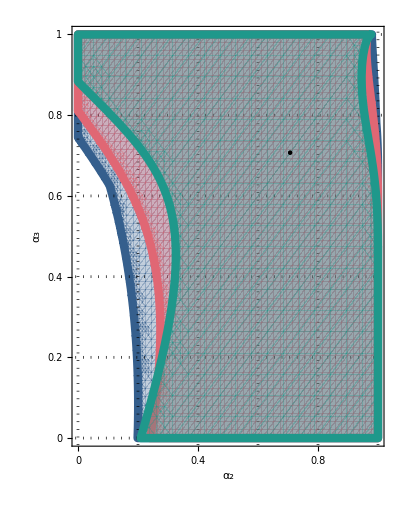

```mathematica
(* Plot witnessed regions. *)

(* Varying α. *)
p3PPTOptimalImperfectCopiesαPlot=Show[RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesατ09[αp22,αp32]<0},{αp22,0,1},{αp32,0,1},PlotRange->{{0,1},{0,1}},PlotTheme->"Detailed",MaxRecursion->7,PlotPoints->50,PlotLegends->None,PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->{Thickness[0.015],PlotColors[[1]]},FrameLabel->{Style["α_2",Black,FontSize->15],Style["α_3",Black,FontSize->15]},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1},None}},FrameStyle->Thickness[0.005],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted]],RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesατ075[αp22,αp32]<0},{αp22,0,1},{αp32,0,1},MaxRecursion->7,PlotPoints->50,PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->{Thickness[0.015],PlotColors[[4]]}],RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesατ06[αp22,αp32]<0},{αp22,0,1},{αp32,0,1},PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->{Thickness[0.015],PlotColors[[2]]}],ListPlot[{{1/Sqrt[2],1/Sqrt[2]}},PlotStyle->{Black,PointSize[Large]}],AspectRatio->1.32,ImageSize->{Automatic,209.5}]
```

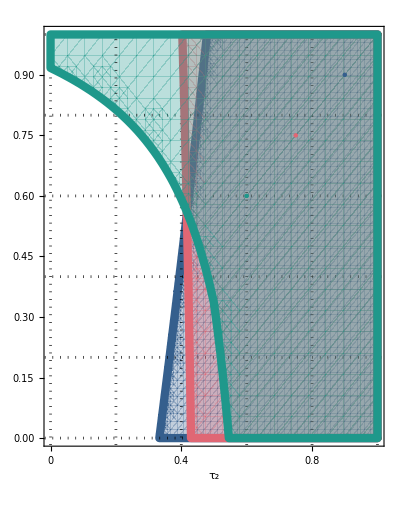

```mathematica
(* Varying τ. *)
p3PPTOptimalImperfectCopiesτPlot=Show[RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesττ09[τp22,τp32]<0},{τp22,0,1},{τp32,0,1},MaxRecursion->7,PlotPoints->50,PlotRange->{{0,1},{0,1}},PlotTheme->"Detailed",MaxRecursion->7,PlotPoints->100,PlotLegends->None,PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->{Thickness[0.015],PlotColors[[1]]},FrameLabel->{Style["τ_2",Black,FontSize->15],None,None,Style["τ_3",Black,FontSize->15]},FrameTicks->{{None},{{0,0.2,0.4,0.6,0.8,1},None}},FrameStyle->Thickness[0.005],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted]],RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesττ075[τp22,τp32]<0},{τp22,0,1},{τp32,0,1},PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->{Thickness[0.015],PlotColors[[4]]}],RegionPlot[{p3PPTOptimalAnalyticImperfectCopiesττ06[τp22,τp32]<0},{τp22,0,1},{τp32,0,1},PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->{Thickness[0.015],PlotColors[[2]]}],ListPlot[{{{0.9,0.9}},{{0.75,0.75}},{{0.6,0.6}}},PlotStyle->{{PlotColors[[1]],PointSize[Large]},{PlotColors[[4]],PointSize[Large]},{PlotColors[[2]],PointSize[Large]}}],AspectRatio->1.32,ImageSize->{Automatic,201.5}]
```

#### Combined plot

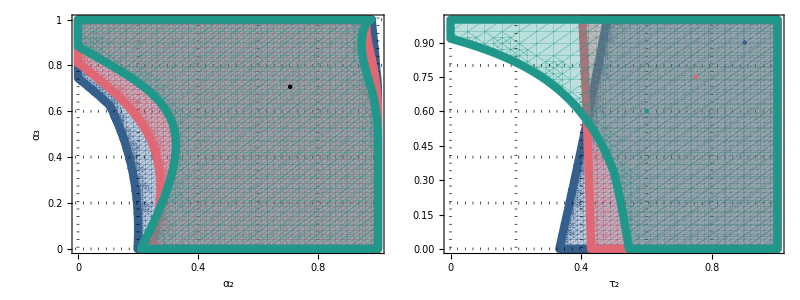
b) Noisy copies
-Graphics-

```mathematica
(* Combine the latter two into a single graphic. *)
p3PPTOptimalImperfectCopiesPlot=Column[{Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["                    b) ",Black,FontSize->15.5,Bold,FontFamily->"Helvetica"],Style["Noisy copies",Black,FontSize->15,FontFamily->"Helvetica"]}],Alignment->Center,ImageSize->240],Grid[{{p3PPTOptimalImperfectCopiesαPlot,p3PPTOptimalImperfectCopiesτPlot}},Alignment->Bottom,Spacings->{0.1}]},Spacings->-0.5]
```

### Required samples

#### Data

```mathematica
(* Define function for the required number of samples. *)
p3PPTQuadraticRequiredSamplesSimple[n_,α_,τ_]:=(1-3 p2^4-2 p2^2 (-2+p3)+√(33 p2^8-4 p2^6 (14+9 p3)+(1+2 p3^2)^2+2 p2^4 (7+8 p3 (3+2 p3))-4 p2^2 (-2+p3 (3+2 p3 (4+p3)))))/(2 (p2^2-p3)^2)/.{p2->p2AnalyticSimple[n,α,τ],p3->p3AnalyticSimple[n,α,τ]};;
```

```mathematica
(* Calculate crossovers in the analytic limit. *)
p3PPTQuadraticAnalyticFixedαSimple=Table[p3PPTQuadraticAnalyticSimple[n,1/Sqrt[2],τ],{n,1,10,1}];
p3PPTQuadraticAnalyticFixedαCrossoversSimple=Table[τ/.NSolve[p3PPTQuadraticAnalyticFixedαSimple[[i]]==0&&0<τ<1,τ,WorkingPrecision->5][[1]],{i,1,Length[p3PPTQuadraticAnalyticFixedαSimple]}];
```

#### Plot

```mathematica
(* Define τ points for N=1. *)
p3PPTOptimalAnalyticRequiredSamplesN1τPoints=Quiet@{{{0.9,p3PPTQuadraticRequiredSamplesSimple[1,1/Sqrt[2],0.9]}},{{0.75,p3PPTQuadraticRequiredSamplesSimple[1,1/Sqrt[2],0.75]}},{{0.6,p3PPTQuadraticRequiredSamplesSimple[1,1/Sqrt[2],0.6]}}};

(* Define corresponding ListPlots. *)
SubfigurecPoints[i_,j_]:=ListLogPlot[p3PPTOptimalAnalyticRequiredSamplesN1τPoints[[i]],PlotStyle->{PointSize[Large],PlotColors[[j]]}];
```

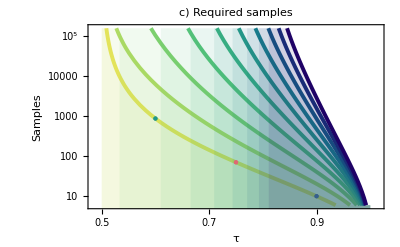

```mathematica
(* Plot the required number of samples as a function of τ for various N. *)
p3PPTQuadraticRequiredSamplesPlot=Show[Table[LogPlot[p3PPTQuadraticRequiredSamplesSimple[n,1/Sqrt[2],τ],{τ,p3PPTQuadraticAnalyticFixedαCrossoversSimple[[n]],1},PlotRange->{{0.485,1.015},{6,160000}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Thickness[0.007],ContinuousColors[n]}},Filling->{1->{0.1,Directive[ContinuousColors[n],Opacity[0.1]]}},FrameLabel->{Style["τ",Black,FontSize->15],Style["Samples",Black,FontSize->15]},FrameTicks->{{{{10,"10^1"},{100,"10^2"},{1000,"10^3"},{10000,"10^4"},{100000,"10^5"}},None},{{0.5,0.6,0.7,0.8,0.9,1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{Join[{0.5,0.6,0.7,0.8,0.9,1},Table[{p3PPTQuadraticAnalyticFixedαCrossoversSimple[[n]],Directive[Dashing[None],Thickness[0.003],ContinuousColors[n]]},{n,1,10}]],{10,100,1000,10000,100000}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["c) ",Black,FontSize->16,Bold],Style["Required samples",Black,FontSize->15]}],Alignment->Center,ImageSize->250]],{n,1,10}],SubfigurecPoints[1,1],SubfigurecPoints[2,4],SubfigurecPoints[3,2],ImageSize->{Automatic,222}]
```

### Combined figure

```mathematica
(* Combine the latter three plots into a single figure. *)
Grid[{{p3PPTOptimalAnalyticLossesPlot,p3PPTOptimalImperfectCopiesPlot,p3PPTQuadraticRequiredSamplesPlot}},Spacings->0.7,Alignment->Bottom]
```

-Graphics- |                     b) Noisy copies
-Graphics- | -Graphics-

### Numerical experiments for N=1

#### Data

```mathematica
(* Generate numerical noisy data for varying τ. List of arguments: α, δα, τ, δτ, number of samples start, end, steps, total repetitions. Takes some time, evaluate only if necessary. *)

(* τ=0.9. *)
p3PPTOptimalNumericalNoisyτ09=p3PPTOptimalNumericalNoisy[1/Sqrt[2],0.05/Sqrt[2],0.9,0.05,50,1000,50,500]
```

```mathematica
(* τ=0.75. *)
p3PPTOptimalNumericalNoisyτ075=p3PPTOptimalNumericalNoisy[1/Sqrt[2],0.05/Sqrt[2],0.75,0.05,50,1000,50,500]
```

```mathematica
(* τ=0.6. *)
p3PPTOptimalNumericalNoisyτ06=p3PPTOptimalNumericalNoisy[1/Sqrt[2],0.05/Sqrt[2],0.6,0.05,50,1000,50,500]
```

```mathematica
(* Set the results as definitions. *)

(* τ=0.9. *)
p3PPTOptimalNumericalNoisyτ09={{50,-0.490.20},{100,-0.480.13},{150,-0.460.11},{200,-0.470.09},{250,-0.470.08},{300,-0.470.08},{350,-0.460.07},{400,-0.480.07},{450,-0.480.06},{500,-0.480.06},{550,-0.470.05},{600,-0.470.05},{650,-0.480.05},{700,-0.470.05},{750,-0.470.05},{800,-0.480.04},{850,-0.470.04},{900,-0.470.04},{950,-0.480.05},{1000,-0.470.04}};

(* τ=0.75. *)
p3PPTOptimalNumericalNoisyτ075={{50,-0.250.22},{100,-0.210.16},{150,-0.200.12},{200,-0.210.10},{250,-0.200.10},{300,-0.210.08},{350,-0.220.08},{400,-0.210.08},{450,-0.210.08},{500,-0.210.07},{550,-0.210.06},{600,-0.210.06},{650,-0.200.06},{700,-0.210.06},{750,-0.200.06},{800,-0.200.05},{850,-0.200.05},{900,-0.210.05},{950,-0.210.05},{1000,-0.210.05}};

(* τ=0.6. *)
p3PPTOptimalNumericalNoisyτ06={{50,-0.060.20},{100,-0.060.13},{150,-0.070.12},{200,-0.060.10},{250,-0.060.10},{300,-0.050.09},{350,-0.060.09},{400,-0.060.07},{450,-0.070.07},{500,-0.050.06},{550,-0.050.06},{600,-0.050.06},{650,-0.060.06},{700,-0.060.05},{750,-0.050.06},{800,-0.050.05},{850,-0.050.05},{900,-0.050.05},{950,-0.050.05},{1000,-0.050.04}};
```

#### Plot

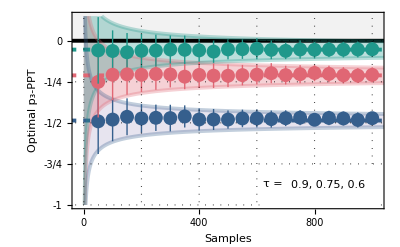

```mathematica
(* Plot the numerical witness against the sample size for different τ. *)
p3PPTOptimalNumericalNoisyPlot=Show[Plot[{0,p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6]},{x,-50,1100},PlotRange->{{-20,1020},{-1,0.15}},PlotTheme->"Detailed",PlotLegends->None,Filling->{1->{0.5,Directive[Gray,Opacity[0.1]]},5->{6},7->{{8},Directive[PlotColorsOpacity[[4]]]},9->{{10},Directive[PlotColorsOpacity[[2]]]}},PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Dashed,PlotColors[[1]]},{Thickness[0.007],Dashed,PlotColors[[4]]},{Thickness[0.007],Dashed,PlotColors[[2]]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[2]]},{Thickness[0.007],PlotColorsOpacity[[2]]}},FrameLabel->{Style["Samples",Black,FontSize->15],Style["Optimal p_3-PPT",Black,FontSize->15]},FrameTicks->{{{-1,{-0.75,"-3/4"},{-0.5,"-1/2"},{-0.25,"-1/4"},0,{0.25,"1/4"}},None},{{0,200,400,600,800,1000},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,200,400,600,800,1000},{-1,-0.75,-0.5,-0.25,0,0.25}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->None],ListPlot[p3PPTOptimalNumericalNoisyτ09,PlotStyle->{PointSize[0.025],PlotColors[[1]]},IntervalMarkers->"Fences"],ListPlot[p3PPTOptimalNumericalNoisyτ075,PlotStyle->{PointSize[0.025],PlotColors[[4]]},IntervalMarkers->"Fences"],ListPlot[p3PPTOptimalNumericalNoisyτ06,PlotStyle->{PointSize[0.025],PlotColors[[2]]},IntervalMarkers->"Fences"],Graphics[{White,Rectangle[{610,-100},{1010,-0.76}],Black,FontSize->15,Text["τ =",{657,-0.875}],FontSize->13,Text[Apply[StringJoin,ToString[#,StandardForm]&/@{Style[" 0.9",PlotColors[[1]]],Style[",",Black],Style[" 0.75",PlotColors[[4]]],Style[",",Black],Style[" 0.6",PlotColors[[2]]]}],{847,-0.88}]}],ImageSize->{Automatic,210}]
```

Appendix plots

### Photon-number distributions

#### Data

```mathematica
(* Generate measurement distributions for various τ as matrices. Start with Subscript[p, 2]. We replace all entries which are strictly 0 by -1 to plot them in white. *)

(* τ=1. *)
PhotonNumbersp2N1τ1Matrix=Table[If[na2+nb2≤2,PhotonNumbersp2N1[na2,nb2,1/Sqrt[2],1/Sqrt[2],1,1],2],{na2,2,0,-1},{nb2,0,2}]/.{0->-1};

(* τ=0.9. *)
PhotonNumbersp2N1τ09Matrix=Table[If[na2+nb2≤2,PhotonNumbersp2N1[na2,nb2,1/Sqrt[2],1/Sqrt[2],0.9,0.9],2],{na2,2,0,-1},{nb2,0,2}]/.{0->-1};

(* τ=0.75. *)
PhotonNumbersp2N1τ075Matrix=Table[If[na2+nb2≤2,PhotonNumbersp2N1[na2,nb2,1/Sqrt[2],1/Sqrt[2],0.75,0.75],2],{na2,2,0,-1},{nb2,0,2}]/.{0->-1};

(* τ=0.6. *)
PhotonNumbersp2N1τ06Matrix=Table[If[na2+nb2≤2,PhotonNumbersp2N1[na2,nb2,1/Sqrt[2],1/Sqrt[2],0.6,0.6],2],{na2,2,0,-1},{nb2,0,2}]/.{0->-1};
```

```mathematica
(* Now Subscript[p, 3]. First, marginalize the full measurement distribution. *)

(* Subsystem A. *)
PhotonNumbersp3N1MarginalA[na2_,na3_,α_,τ_]=Sum[PhotonNumbersp3N1[na2,nb2,na3,nb3,α,α,α,τ,τ,τ],{nb2,0,3},{nb3,0,3}];

(* Modes 2. *)
PhotonNumbersp3N1Marginal2[na2_,nb2_,α_,τ_]=Sum[PhotonNumbersp3N1[na2,nb2,na3,nb3,α,α,α,τ,τ,τ],{na3,0,3},{nb3,0,3}];
```

```mathematica
(* Generate measurement distributions for various τ as matrices, both for subsystem A and modes 2. *)

(* Subsystem A. *)

(* τ=1. *)
PhotonNumbersp3N1τ1MarginalAMatrix=Table[If[na2+na3≤3,PhotonNumbersp3N1MarginalA[na2,na3,1/Sqrt[2],1],2],{na2,3,0,-1},{na3,0,3}]/.{0->-1};

(* τ=0.9. *)
PhotonNumbersp3N1τ09MarginalAMatrix=Table[If[na2+na3≤3,PhotonNumbersp3N1MarginalA[na2,na3,1/Sqrt[2],0.9],2],{na2,3,0,-1},{na3,0,3}]/.{0->-1};

(* τ=0.75. *)
PhotonNumbersp3N1τ075MarginalAMatrix=Table[If[na2+na3≤3,PhotonNumbersp3N1MarginalA[na2,na3,1/Sqrt[2],0.75],2],{na2,3,0,-1},{na3,0,3}]/.{0->-1};

(* τ=0.6. *)
PhotonNumbersp3N1τ06MarginalAMatrix=Table[If[na2+na3≤3,PhotonNumbersp3N1MarginalA[na2,na3,1/Sqrt[2],0.6],2],{na2,3,0,-1},{na3,0,3}]/.{0->-1};
```

```mathematica
(* Modes 2. *)

(* τ=1. *)
PhotonNumbersp3N1τ1Marginal2Matrix=Table[If[na2+nb2≤3,PhotonNumbersp3N1Marginal2[na2,nb2,1/Sqrt[2],1],2],{na2,3,0,-1},{nb2,0,3}]/.{0->-1};

(* τ=0.9. *)
PhotonNumbersp3N1τ09Marginal2Matrix=Table[If[na2+nb2≤3,PhotonNumbersp3N1Marginal2[na2,nb2,1/Sqrt[2],0.9],2],{na2,3,0,-1},{nb2,0,3}]/.{0->-1};

(* τ=0.75. *)
PhotonNumbersp3N1τ075Marginal2Matrix=Table[If[na2+nb2≤3,PhotonNumbersp3N1Marginal2[na2,nb2,1/Sqrt[2],0.75],2],{na2,3,0,-1},{nb2,0,3}]/.{0->-1};

(* τ=0.6. *)
PhotonNumbersp3N1τ06Marginal2Matrix=Table[If[na2+nb2≤3,PhotonNumbersp3N1Marginal2[na2,nb2,1/Sqrt[2],0.6],2],{na2,3,0,-1},{nb2,0,3}]/.{0->-1};
```

#### Circuit for purity p_2

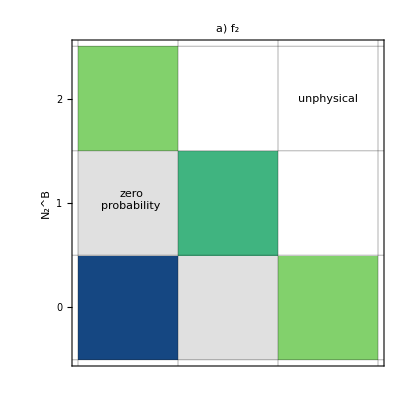

```mathematica
(* Plot the distributions. *)

(* τ=1. *)
PhotonNumbersp2N1τ1Plot=Show[MatrixPlot[PhotonNumbersp2N1τ1Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{3,"0"},{2,"1"},{1,"2"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3},{0,1,2,3}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["a) ",Black,FontSize->16,Bold],Style["f_2",Black,FontSize->15]}],Alignment->Center,ImageSize->250],PlotLegends->None],Graphics[{Black,FontSize->13,Text["unphysical",{2.5,2.5},Automatic,{1,-1}],Text["zero
probability",{0.53,1.53},Automatic,{1,-1}]}],ImageSize->{Automatic,230}]
```

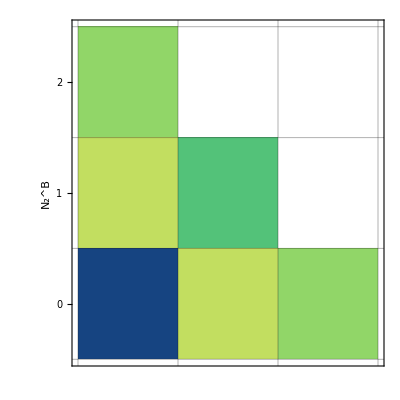

```mathematica
(* τ=0.9. *)
PhotonNumbersp2N1τ09Plot=MatrixPlot[PhotonNumbersp2N1τ09Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{3,"0"},{2,"1"},{1,"2"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3},{0,1,2,3}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

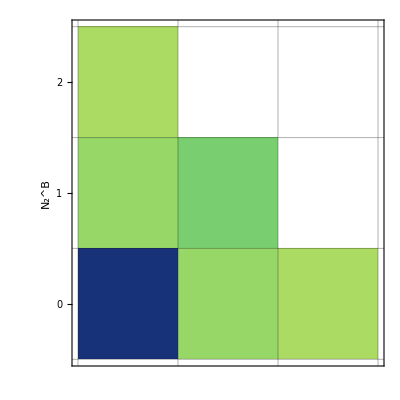

```mathematica
(* τ=0.75. *)
PhotonNumbersp2N1τ075Plot=MatrixPlot[PhotonNumbersp2N1τ075Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{3,"0"},{2,"1"},{1,"2"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3},{0,1,2,3}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

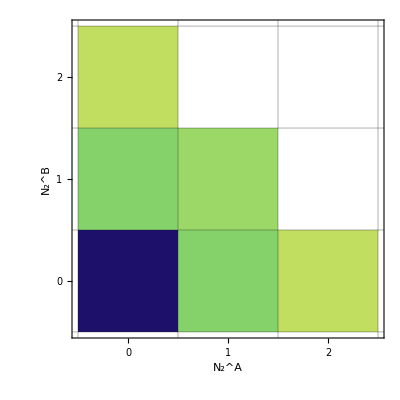

```mathematica
(* τ=0.6. *)
PhotonNumbersp2N1τ06Plot=MatrixPlot[PhotonNumbersp2N1τ06Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{3,"0"},{2,"1"},{1,"2"}},{{1,"0"},{2,"1"},{3,"2"}}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3},{0,1,2,3}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16],Style["N_2^A",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,260}]
```

#### Circuit for third PT-moment p_3: subsystem A

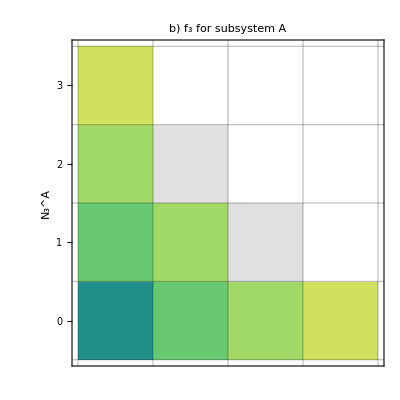

```mathematica
(* Plot the distributions. *)

(* Subsystem A. *)

(* τ=1. *)
PhotonNumbersp3N1τ1MarginalAPlot=MatrixPlot[PhotonNumbersp3N1τ1MarginalAMatrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_3^A",Black,FontSize->16]},PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["b) ",Black,FontSize->16,Bold],Style["f_3 for subsystem A",Black,FontSize->15]}],Alignment->Center,ImageSize->250],PlotLegends->None,ImageSize->{Automatic,230}]
```

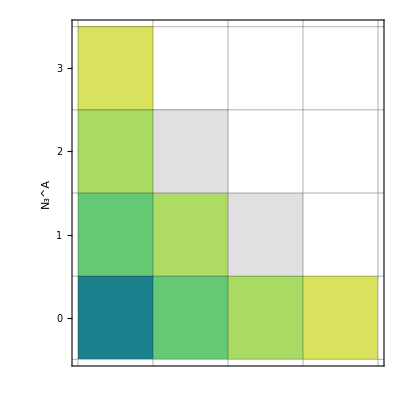

```mathematica
(* τ=0.9. *)
PhotonNumbersp3N1τ09MarginalAPlot=MatrixPlot[PhotonNumbersp3N1τ09MarginalAMatrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_3^A",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

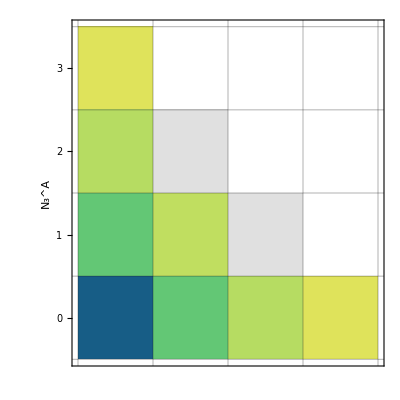

```mathematica
(* τ=0.75. *)
PhotonNumbersp3N1τ075MarginalAPlot=MatrixPlot[PhotonNumbersp3N1τ075MarginalAMatrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_3^A",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

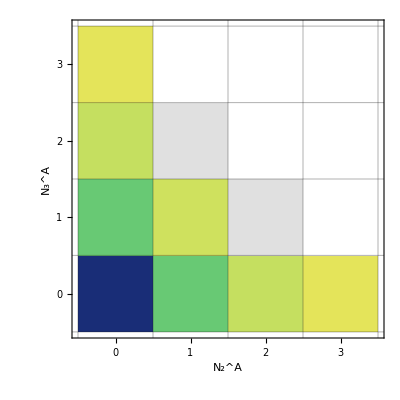

```mathematica
(* τ=0.6. *)
PhotonNumbersp3N1τ06MarginalAPlot=MatrixPlot[PhotonNumbersp3N1τ06MarginalAMatrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},{{1,"0"},{2,"1"},{3,"2"},{4,"3"}}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_3^A",Black,FontSize->16],Style["N_2^A",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,260}]
```

#### Circuit for third PT-moment p_3: modes 2

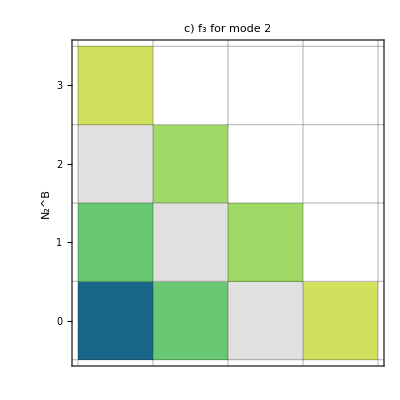

```mathematica
(* Modes 2. *)

(* τ=1. *)
PhotonNumbersp3N1τ1Marginal2Plot=MatrixPlot[PhotonNumbersp3N1τ1Marginal2Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},ClippingStyle->White,PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["c) ",Black,FontSize->16,Bold],Style["f_3 for mode 2",Black,FontSize->15]}],Alignment->Center,ImageSize->250],PlotLegends->None,ImageSize->{Automatic,230}]
```

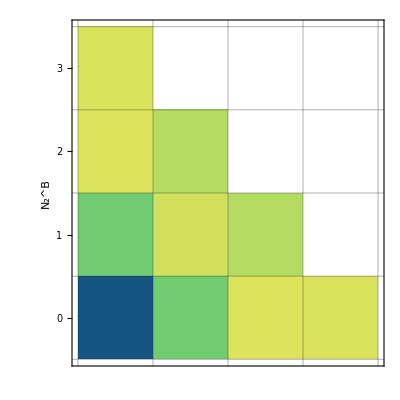

```mathematica
(* Modes 2. *)

(* τ=0.9. *)
PhotonNumbersp3N1τ09Marginal2Plot=MatrixPlot[PhotonNumbersp3N1τ09Marginal2Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},ClippingStyle->White,PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

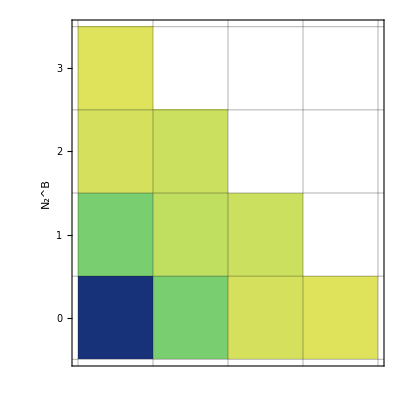

```mathematica
(* Modes 2. *)

(* τ=0.75. *)
PhotonNumbersp3N1τ075Marginal2Plot=MatrixPlot[PhotonNumbersp3N1τ075Marginal2Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},ClippingStyle->White,PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},None},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,213}]
```

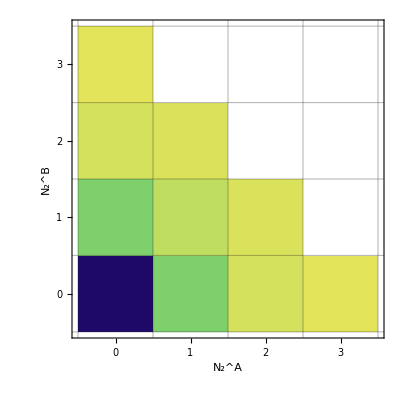

```mathematica
(* Modes 2. *)

(* τ=0.6. *)
PhotonNumbersp3N1τ06Marginal2Plot=MatrixPlot[PhotonNumbersp3N1τ06Marginal2Matrix,PlotTheme->"Detailed",ColorFunction->ContinuousColors2,ColorFunctionScaling->False,ClippingStyle->{GrayLevel[0.88],White},PlotRange->{0,1},FrameTicks->{{{4,"0"},{3,"1"},{2,"2"},{1,"3"}},{{1,"0"},{2,"1"},{3,"2"},{4,"3"}}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,1,2,3,4},{0,1,2,3,4}},GridLinesStyle->Directive[GrayLevel[0.1],Thickness[0.002],Opacity[0.3]],FrameLabel->{Style["N_2^B",Black,FontSize->16],Style["N_2^A",Black,FontSize->16]},PlotLegends->None,ImageSize->{Automatic,260}]
```

#### Combined figure

```mathematica
(* Define a function for the labels. *)
Labelτ[τ_,h_]:=Graphics[{White,Rectangle[{0,0},{1,1}],FontSize->16,Black,Text[Style["τ="<>ToString[τ],Bold],{0,h},Automatic,{0,1}]},ImageSize->{30,100}];
```

```mathematica
(* Combine the latter nine plots into a single figure. *)
Legended[Grid[{{Labelτ[1,-0.8],PhotonNumbersp2N1τ1Plot,PhotonNumbersp3N1τ1MarginalAPlot,PhotonNumbersp3N1τ1Marginal2Plot},{Labelτ[0.9,-0.2],PhotonNumbersp2N1τ09Plot,PhotonNumbersp3N1τ09MarginalAPlot,PhotonNumbersp3N1τ09Marginal2Plot},{Labelτ[0.75,-0.2],PhotonNumbersp2N1τ075Plot,PhotonNumbersp3N1τ075MarginalAPlot,PhotonNumbersp3N1τ075Marginal2Plot},{Labelτ[0.6,3.3],PhotonNumbersp2N1τ06Plot,PhotonNumbersp3N1τ06MarginalAPlot,PhotonNumbersp3N1τ06Marginal2Plot},{},{},{}},Spacings->{-0.25,0.4},Alignment->{Left,Center}],Placed[BarLegend[{ContinuousColors2,{0,0.6}},LabelStyle->{Black,FontSize->13},LegendLayout->"Row",LegendMarkerSize->250],{0.541,0}]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
 |  |  | 
 |  |  |

### Error of the mean I: Varying sample size

#### Data

```mathematica
(* Generate numerical data for varying τ. List of arguments: αp21, αp22, αp31, αp32, αp33, τp21, τp22, τp31, τp32, τp33, number of samples start, end, steps, total repetitions. Takes some time, evaluate only if necessary. *)

(* τ=1. *)
p3PPTAllNumericalτ1=p3PPTAllNumerical[1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1,1,1,1,1,50,1000,50,500]
```

```mathematica
(* τ=0.9. *)
p3PPTAllNumericalτ09=p3PPTAllNumerical[1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],0.9,0.9,0.9,0.9,0.9,50,1000,50,500]
```

```mathematica
(* τ=0.75. *)
p3PPTAllNumericalτ075=p3PPTAllNumerical[1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],0.75,0.75,0.75,0.75,0.75,50,1000,50,500]
```

```mathematica
(* τ=0.6. *)
p3PPTAllNumericalτ06=p3PPTAllNumerical[1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],0.6,0.6,0.6,0.6,0.6,50,1000,50,500]
```

```mathematica
(* Set the results as definitions. *)

(* τ=1. *)
p3PPTAllNumericalτ1={{50,{-0.760.14},{-0.760.14},{-0.760.14}},{100,{-0.740.10},{-0.740.10},{-0.740.10}},{150,{-0.750.08},{-0.750.08},{-0.750.08}},{200,{-0.750.07},{-0.750.07},{-0.750.07}},{250,{-0.740.06},{-0.740.06},{-0.740.06}},{300,{-0.750.06},{-0.750.06},{-0.750.06}},{350,{-0.750.05},{-0.750.05},{-0.750.05}},{400,{-0.750.05},{-0.750.05},{-0.750.05}},{450,{-0.750.05},{-0.750.05},{-0.750.05}},{500,{-0.750.04},{-0.750.04},{-0.750.04}},{550,{-0.750.04},{-0.750.04},{-0.750.04}},{600,{-0.750.04},{-0.750.04},{-0.750.04}},{650,{-0.750.04},{-0.750.04},{-0.750.04}},{700,{-0.750.04},{-0.750.04},{-0.750.04}},{750,{-0.750.04},{-0.750.04},{-0.750.04}},{800,{-0.7450.034},{-0.7450.034},{-0.7450.034}},{850,{-0.7500.034},{-0.7500.034},{-0.7500.034}},{900,{-0.7480.032},{-0.7480.032},{-0.7480.032}},{950,{-0.7490.030},{-0.7490.030},{-0.7490.030}},{1000,{-0.7480.032},{-0.7480.032},{-0.7480.032}}};

(* τ=0.9. *)
p3PPTAllNumericalτ09={{50,{-0.490.19},{-0.440.20},{-0.490.19}},{100,{-0.470.13},{-0.420.13},{-0.470.13}},{150,{-0.480.11},{-0.420.11},{-0.480.11}},{200,{-0.490.09},{-0.430.09},{-0.490.09}},{250,{-0.500.08},{-0.440.08},{-0.500.08}},{300,{-0.490.08},{-0.440.08},{-0.490.08}},{350,{-0.490.06},{-0.430.06},{-0.490.06}},{400,{-0.480.06},{-0.420.07},{-0.480.06}},{450,{-0.480.06},{-0.430.07},{-0.480.06}},{500,{-0.490.05},{-0.430.06},{-0.490.05}},{550,{-0.480.06},{-0.430.06},{-0.480.06}},{600,{-0.480.05},{-0.420.06},{-0.480.05}},{650,{-0.490.05},{-0.430.05},{-0.490.05}},{700,{-0.490.05},{-0.430.05},{-0.490.05}},{750,{-0.490.05},{-0.430.05},{-0.490.05}},{800,{-0.490.04},{-0.430.05},{-0.490.04}},{850,{-0.480.04},{-0.420.05},{-0.480.04}},{900,{-0.490.04},{-0.430.04},{-0.490.04}},{950,{-0.480.04},{-0.420.04},{-0.480.04}},{1000,{-0.480.04},{-0.420.04},{-0.480.04}}};

(* τ=0.75. *)
p3PPTAllNumericalτ075={{50,{-0.220.23},{-0.180.21},{-0.230.22}},{100,{-0.230.15},{-0.190.14},{-0.230.15}},{150,{-0.180.12},{-0.140.11},{-0.180.12}},{200,{-0.200.11},{-0.160.10},{-0.200.11}},{250,{-0.200.09},{-0.160.08},{-0.200.09}},{300,{-0.210.09},{-0.160.08},{-0.210.09}},{350,{-0.200.08},{-0.160.07},{-0.200.08}},{400,{-0.220.08},{-0.170.07},{-0.220.08}},{450,{-0.210.07},{-0.160.06},{-0.210.07}},{500,{-0.200.07},{-0.150.06},{-0.200.07}},{550,{-0.210.06},{-0.170.06},{-0.210.06}},{600,{-0.210.06},{-0.170.05},{-0.210.06}},{650,{-0.210.06},{-0.170.05},{-0.210.06}},{700,{-0.210.05},{-0.170.05},{-0.210.05}},{750,{-0.210.06},{-0.160.05},{-0.210.06}},{800,{-0.210.05},{-0.170.05},{-0.210.05}},{850,{-0.210.06},{-0.160.05},{-0.210.06}},{900,{-0.210.05},{-0.160.05},{-0.210.05}},{950,{-0.210.05},{-0.160.04},{-0.210.05}},{1000,{-0.210.05},{-0.170.05},{-0.210.05}}};

(* τ=0.6. *)
p3PPTAllNumericalτ06={{50,{0.000.20},{-0.010.16},{-0.030.17}},{100,{-0.060.18},{-0.060.15},{-0.080.16}},{150,{-0.050.13},{-0.050.10},{-0.070.11}},{200,{-0.070.12},{-0.060.10},{-0.080.10}},{250,{-0.070.10},{-0.060.08},{-0.070.09}},{300,{-0.070.09},{-0.060.08},{-0.070.08}},{350,{-0.060.09},{-0.050.07},{-0.070.08}},{400,{-0.060.08},{-0.060.06},{-0.070.07}},{450,{-0.040.08},{-0.030.06},{-0.050.07}},{500,{-0.070.07},{-0.060.06},{-0.070.06}},{550,{-0.050.07},{-0.040.06},{-0.060.07}},{600,{-0.050.06},{-0.040.05},{-0.050.05}},{650,{-0.060.06},{-0.050.05},{-0.060.06}},{700,{-0.060.07},{-0.050.05},{-0.060.06}},{750,{-0.060.06},{-0.050.05},{-0.060.06}},{800,{-0.060.05},{-0.050.05},{-0.060.05}},{850,{-0.050.06},{-0.040.05},{-0.050.05}},{900,{-0.050.06},{-0.040.05},{-0.050.05}},{950,{-0.050.06},{-0.040.04},{-0.050.05}},{1000,{-0.060.05},{-0.050.04},{-0.070.05}}};
```

```mathematica
(* Extract the individual criteria. *)

(* Linear. *)
p3PPTLinearNumericalτ1=Table[{p3PPTAllNumericalτ1[[i,1]],p3PPTAllNumericalτ1[[i,2,1]]},{i,1,Length[p3PPTAllNumericalτ1]}];
p3PPTLinearNumericalτ09=Table[{p3PPTAllNumericalτ09[[i,1]],p3PPTAllNumericalτ09[[i,2,1]]},{i,1,Length[p3PPTAllNumericalτ09]}];
p3PPTLinearNumericalτ075=Table[{p3PPTAllNumericalτ075[[i,1]],p3PPTAllNumericalτ075[[i,2,1]]},{i,1,Length[p3PPTAllNumericalτ075]}];
p3PPTLinearNumericalτ06=Table[{p3PPTAllNumericalτ06[[i,1]],p3PPTAllNumericalτ06[[i,2,1]]},{i,1,Length[p3PPTAllNumericalτ06]}];

(* Quadratic. *)
p3PPTQuadraticNumericalτ1=Table[{p3PPTAllNumericalτ1[[i,1]],p3PPTAllNumericalτ1[[i,3,1]]},{i,1,Length[p3PPTAllNumericalτ1]}];
p3PPTQuadraticNumericalτ09=Table[{p3PPTAllNumericalτ09[[i,1]],p3PPTAllNumericalτ09[[i,3,1]]},{i,1,Length[p3PPTAllNumericalτ09]}];
p3PPTQuadraticNumericalτ075=Table[{p3PPTAllNumericalτ075[[i,1]],p3PPTAllNumericalτ075[[i,3,1]]},{i,1,Length[p3PPTAllNumericalτ075]}];
p3PPTQuadraticNumericalτ06=Table[{p3PPTAllNumericalτ06[[i,1]],p3PPTAllNumericalτ06[[i,3,1]]},{i,1,Length[p3PPTAllNumericalτ06]}];

(* Optimal. *)
p3PPTOptimalNumericalτ1=Table[{p3PPTAllNumericalτ1[[i,1]],p3PPTAllNumericalτ1[[i,4,1]]},{i,1,Length[p3PPTAllNumericalτ1]}];
p3PPTOptimalNumericalτ09=Table[{p3PPTAllNumericalτ09[[i,1]],p3PPTAllNumericalτ09[[i,4,1]]},{i,1,Length[p3PPTAllNumericalτ09]}];
p3PPTOptimalNumericalτ075=Table[{p3PPTAllNumericalτ075[[i,1]],p3PPTAllNumericalτ075[[i,4,1]]},{i,1,Length[p3PPTAllNumericalτ075]}];
p3PPTOptimalNumericalτ06=Table[{p3PPTAllNumericalτ06[[i,1]],p3PPTAllNumericalτ06[[i,4,1]]},{i,1,Length[p3PPTAllNumericalτ06]}];
```

#### Individual plots

```mathematica
(* Set up nice plotmarkers. *)
NumericalPlotMarkersInternal={NicePlotmarkers[9,0.18,White,PlotColors[[1]],2],NicePlotmarkers[9,0.18,White,PlotColors[[4]],3],NicePlotmarkers[7,0.15,White,PlotColors[[2]],4]};
```

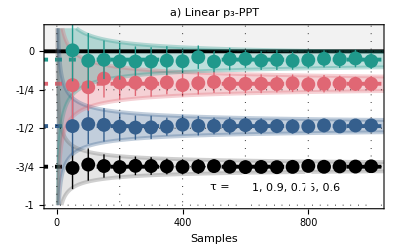

```mathematica
(* Plot the linear numerical witness against the sample size for different τ. *)
p3PPTLinearNumericalPlot=Show[Plot[{0,p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.99999],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.99999]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.99999]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],
p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.9]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.75]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.6]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6]},{x,-50,1100},PlotRange->{{-20,1020},{-1,0.15}},PlotTheme->"Detailed",PlotLegends->None,Filling->{1->{0.5,Directive[Gray,Opacity[0.1]]},6->{{7},Directive[{Gray,Opacity[0.2]}]},8->{{9},Directive[PlotColorsOpacity[[1]]]},10->{{11},Directive[PlotColorsOpacity[[4]]]},12->{{13},Directive[PlotColorsOpacity[[2]]]}},PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Black,Dashed},{Thickness[0.007],Dashed,PlotColors[[1]]},{Thickness[0.007],Dashed,PlotColors[[4]]},{Thickness[0.007],Dashed,PlotColors[[2]]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[2]]},{Thickness[0.007],PlotColorsOpacity[[2]]}},FrameLabel->{Style["Samples",Black,FontSize->15]},FrameTicks->{{{-1,{-0.75,"-3/4"},{-0.5,"-1/2"},{-0.25,"-1/4"},0,{0.25,"1/4"}},None},{{0,200,400,600,800,1000},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,200,400,600,800,1000},{-1,-0.75,-0.5,-0.25,0,0.25}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["a) ",Black,FontSize->16,Bold],Style["Linear p_3-PPT",Black,FontSize->15]}],Alignment->Center,ImageSize->250]],ListPlot[p3PPTLinearNumericalτ1,PlotStyle->{PointSize[0.025],Black},IntervalMarkers->"Fences"],ListPlot[p3PPTLinearNumericalτ09,PlotStyle->{PointSize[0.025],PlotColors[[1]]},IntervalMarkers->"Fences"],ListPlot[p3PPTLinearNumericalτ075,PlotStyle->{PointSize[0.025],PlotColors[[4]]},IntervalMarkers->"Fences"],ListPlot[p3PPTLinearNumericalτ06,PlotStyle->{PointSize[0.025],PlotColors[[2]]},IntervalMarkers->"Fences"],Graphics[{White,Rectangle[{590,-100},{610,-0.8}],Rectangle[{790,-100},{810,-0.792}],Rectangle[{990,-100},{1010,-0.792}],Black,FontSize->15,Text["τ =",{520,-0.885}],FontSize->13,Text[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["1",Black],Style[",",Black],Style[" 0.9",PlotColors[[1]]],Style[",",Black],Style[" 0.75",PlotColors[[4]]],Style[",",Black],Style[" 0.6",PlotColors[[2]]]}],{760,-0.89}]}],ImageSize->{Automatic,220}]
```

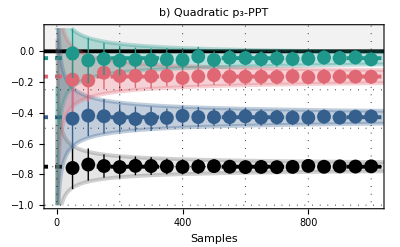

```mathematica
(* The same for the quadratic criterion. *)
p3PPTQuadraticNumericalPlot=Quiet@Show[Plot[{0,p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.99999],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.9],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.75],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.6],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.99999]+p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.99999]-p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],
p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.9]+p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.9]-p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.75]+p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.75]-p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.6]+p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.6],p3PPTQuadraticAnalyticSimple[1,1/Sqrt[2],0.6]-p3PPTQuadraticAnalyticErrorSimple[x,1,1/Sqrt[2],0.6]},{x,-50,1100},PlotRange->{{-20,1020},{-1,0.15}},PlotTheme->"Detailed",PlotLegends->None,Filling->{1->{0.5,Directive[Gray,Opacity[0.1]]},6->{{7},Directive[{Gray,Opacity[0.2]}]},8->{{9},Directive[PlotColorsOpacity[[1]]]},10->{{11},Directive[PlotColorsOpacity[[4]]]},12->{{13},Directive[PlotColorsOpacity[[2]]]}},PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Black,Dashed},{Thickness[0.007],Dashed,PlotColors[[1]]},{Thickness[0.007],Dashed,PlotColors[[4]]},{Thickness[0.007],Dashed,PlotColors[[2]]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[2]]},{Thickness[0.007],PlotColorsOpacity[[2]]}},FrameLabel->{Style["Samples",Black,FontSize->15]},FrameTicks->{{None},{{0,200,400,600,800,1000},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,200,400,600,800,1000},{-1,-0.75,-0.5,-0.25,0,0.25}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["b) ",Black,FontSize->16,Bold],Style["Quadratic p_3-PPT",Black,FontSize->15]}],Alignment->Center,ImageSize->250]],ListPlot[p3PPTQuadraticNumericalτ1,PlotStyle->{PointSize[0.025],Black},IntervalMarkers->"Fences"],ListPlot[p3PPTQuadraticNumericalτ09,PlotStyle->{PointSize[0.025],PlotColors[[1]]},IntervalMarkers->"Fences"],ListPlot[p3PPTQuadraticNumericalτ075,PlotStyle->{PointSize[0.025],PlotColors[[4]]},IntervalMarkers->"Fences"],ListPlot[p3PPTQuadraticNumericalτ06,PlotStyle->{PointSize[0.025],PlotColors[[2]]},IntervalMarkers->"Fences"],ImageSize->{Automatic,221}]
```

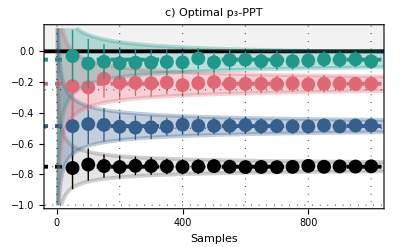

```mathematica
(* The same for the optimal criterion. *)
p3PPTOptimalNumericalPlot=Quiet@Show[Plot[{0,p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.99999],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.9],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.75],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.6],p3PPTLinearAnalyticSimple[1,1/Sqrt[2],0.99999]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.99999]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.99999],
p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.9]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.9]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.9],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.75]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.75]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.75],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.6]+p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6],p3PPTOptimalAnalyticSimple[1,1/Sqrt[2],0.6]-p3PPTLinearAnalyticErrorSimple[x,1,1/Sqrt[2],0.6]},{x,-50,1100},PlotRange->{{-20,1020},{-1,0.15}},PlotTheme->"Detailed",PlotLegends->None,Filling->{1->{0.5,Directive[Gray,Opacity[0.1]]},6->{{7},Directive[{Gray,Opacity[0.2]}]},8->{{9},Directive[PlotColorsOpacity[[1]]]},10->{{11},Directive[PlotColorsOpacity[[4]]]},12->{{13},Directive[PlotColorsOpacity[[2]]]}},PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Black,Dashed},{Thickness[0.007],Dashed,PlotColors[[1]]},{Thickness[0.007],Dashed,PlotColors[[4]]},{Thickness[0.007],Dashed,PlotColors[[2]]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],GrayLevel[0.4],Opacity[0.3]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[1]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[4]]},{Thickness[0.007],PlotColorsOpacity[[2]]},{Thickness[0.007],PlotColorsOpacity[[2]]}},FrameLabel->{Style["Samples",Black,FontSize->15]},FrameTicks->{{None},{{0,200,400,600,800,1000},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,200,400,600,800,1000},{-1,-0.75,-0.5,-0.25,0,0.25}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["c) ",Black,FontSize->16,Bold],Style["Optimal p_3-PPT",Black,FontSize->15]}],Alignment->Center,ImageSize->250]],ListPlot[p3PPTOptimalNumericalτ1,PlotStyle->{PointSize[0.025],Black},IntervalMarkers->"Fences"],ListPlot[p3PPTOptimalNumericalτ09,PlotStyle->{PointSize[0.025],PlotColors[[1]]},IntervalMarkers->"Fences"],ListPlot[p3PPTOptimalNumericalτ075,PlotStyle->{PointSize[0.025],PlotColors[[4]]},IntervalMarkers->"Fences"],ListPlot[p3PPTOptimalNumericalτ06,PlotStyle->{PointSize[0.025],PlotColors[[2]]},IntervalMarkers->"Fences"],ImageSize->{Automatic,220}]
```

#### Combined plot

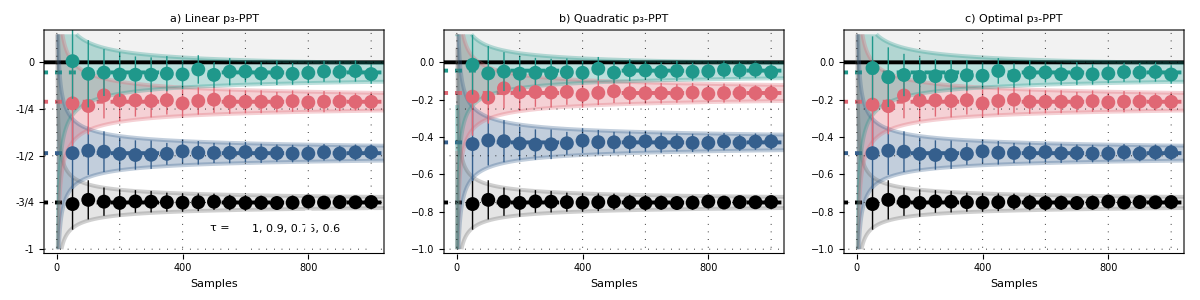

```mathematica
(* Combine the latter three into a single plot. *)
p3PPTAllNumericalPlot=Grid[{{p3PPTLinearNumericalPlot,p3PPTQuadraticNumericalPlot,p3PPTOptimalNumericalPlot}},Alignment->Bottom,Spacings->0.3]
```

### Error of the mean II: Varying τ

#### Data

```mathematica
(* Compute all witnesses over the same sampled data set for dense values of τ. *)
p3PPTAllErrorModel=Table[{τ,p3PPTAllNumerical[1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],1/Sqrt[2],τ,τ,τ,τ,τ,2000,2000,1,200]},{τ,0.02,1,0.02}]
```

```mathematica
(* Set the result as definition. *)
p3PPTAllErrorModel={{0.02,{{2000,{0.0000.011},{0.0180.013},{0.0000.011}}}},{0.04,{{2000,{0.0000.016},{0.0330.019},{0.0000.016}}}},{0.06,{{2000,{0.0030.020},{0.0470.022},{0.0030.020}}}},{0.08,{{2000,{0.0030.023},{0.0550.025},{0.0030.023}}}},{0.1,{{2000,{0.0060.024},{0.0630.025},{0.0060.024}}}},{0.12000000000000001,{{2000,{0.0080.027},{0.0690.028},{0.0080.027}}}},{0.13999999999999999,{{2000,{0.0090.029},{0.0710.029},{0.0090.029}}}},{0.16,{{2000,{0.0130.029},{0.0750.029},{0.0130.029}}}},{0.18,{{2000,{0.0160.029},{0.0760.028},{0.0160.029}}}},{0.19999999999999998,{{2000,{0.0210.031},{0.0780.029},{0.0210.031}}}},{0.22,{{2000,{0.0210.031},{0.0740.028},{0.0210.031}}}},{0.24,{{2000,{0.0220.031},{0.0710.028},{0.0220.031}}}},{0.26,{{2000,{0.0250.032},{0.0690.028},{0.0250.032}}}},{0.28,{{2000,{0.0270.032},{0.0650.028},{0.0270.032}}}},{0.30000000000000004,{{2000,{0.0300.033},{0.0620.028},{0.0300.033}}}},{0.32,{{2000,{0.0300.035},{0.0570.030},{0.0300.035}}}},{0.34,{{2000,{0.0250.035},{0.0480.030},{0.0250.035}}}},{0.36000000000000004,{{2000,{0.0270.034},{0.0450.028},{0.0270.034}}}},{0.38,{{2000,{0.0250.035},{0.0390.029},{0.0250.035}}}},{0.4,{{2000,{0.0290.034},{0.0370.028},{0.0270.032}}}},{0.42000000000000004,{{2000,{0.020.04},{0.0250.030},{0.0160.034}}}},{0.44,{{2000,{0.020.04},{0.0190.030},{0.0130.033}}}},{0.46,{{2000,{0.010.04},{0.0130.029},{0.0070.032}}}},{0.48000000000000004,{{2000,{0.0070.035},{0.0070.028},{0.0010.030}}}},{0.5,{{2000,{0.0000.035},{0.0000.028},{-0.0050.030}}}},{0.52,{{2000,{0.000.04},{-0.0070.029},{-0.0120.032}}}},{0.54,{{2000,{-0.0170.034},{-0.0160.028},{-0.0210.030}}}},{0.56,{{2000,{-0.030.04},{-0.0230.029},{-0.0300.033}}}},{0.5800000000000001,{{2000,{-0.040.04},{-0.0340.030},{-0.0420.034}}}},{0.6,{{2000,{-0.050.04},{-0.0450.030},{-0.0560.035}}}},{0.62,{{2000,{-0.070.04},{-0.0560.030},{-0.0700.035}}}},{0.64,{{2000,{-0.090.04},{-0.0690.030},{-0.090.04}}}},{0.66,{{2000,{-0.1060.035},{-0.0830.030},{-0.1060.035}}}},{0.68,{{2000,{-0.120.04},{-0.0960.031},{-0.120.04}}}},{0.7000000000000001,{{2000,{-0.150.04},{-0.1140.031},{-0.150.04}}}},{0.7200000000000001,{{2000,{-0.170.04},{-0.1320.031},{-0.170.04}}}},{0.74,{{2000,{-0.1960.034},{-0.1520.030},{-0.1960.034}}}},{0.76,{{2000,{-0.2260.033},{-0.1770.030},{-0.2260.033}}}},{0.78,{{2000,{-0.2550.033},{-0.2010.030},{-0.2550.033}}}},{0.8,{{2000,{-0.2860.032},{-0.2290.031},{-0.2860.032}}}},{0.8200000000000001,{{2000,{-0.3250.031},{-0.2650.030},{-0.3250.031}}}},{0.8400000000000001,{{2000,{-0.3600.031},{-0.2980.031},{-0.3600.031}}}},{0.86,{{2000,{-0.3990.031},{-0.3370.031},{-0.3990.031}}}},{0.88,{{2000,{-0.4430.030},{-0.3820.030},{-0.4430.030}}}},{0.9,{{2000,{-0.4860.029},{-0.4290.030},{-0.4860.029}}}},{0.92,{{2000,{-0.5340.027},{-0.4820.029},{-0.5340.027}}}},{0.9400000000000001,{{2000,{-0.5840.026},{-0.5410.028},{-0.5840.026}}}},{0.9600000000000001,{{2000,{-0.6360.025},{-0.6040.027},{-0.6360.025}}}},{0.98,{{2000,{-0.6900.024},{-0.6720.025},{-0.6900.024}}}},{1.,{{2000,{-0.7520.021},{-0.7520.021},{-0.7520.021}}}}};
```

```mathematica
(* Extract the errors for each criterion. *)
p3PPTLinearErrorModel=Table[{p3PPTAllErrorModel[[i,1]],p3PPTAllErrorModel[[i,2,1,2,1,2]]},{i,1,Length[p3PPTAllErrorModel]}];
p3PPTQuadraticErrorModel=Table[{p3PPTAllErrorModel[[i,1]],p3PPTAllErrorModel[[i,2,1,3,1,2]]},{i,1,Length[p3PPTAllErrorModel]}];
p3PPTOptimalErrorModel=Table[{p3PPTAllErrorModel[[i,1]],p3PPTAllErrorModel[[i,2,1,4,1,2]]},{i,1,Length[p3PPTAllErrorModel]}];
```

#### Plot

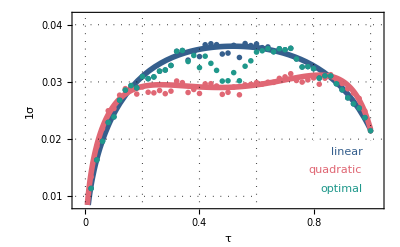

```mathematica
(* Plot the standard deviation as a function of τ for all three criteria. *)
Show[Plot[{p3PPTLinearAnalyticErrorSimple[2000,1,1/Sqrt[2],τ],p3PPTQuadraticAnalyticErrorSimple[2000,1,1/Sqrt[2],τ]},{τ,0,1},PlotRange->{{-0.026,1.026},{0.0085,0.0415}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Thickness[0.01],PlotColors[[1]]},{Thickness[0.01],PlotColors[[4]]}},FrameLabel->{Style["τ",Black,FontSize->15],Style["1σ",Black,FontSize->15]},FrameTicks->{{{0.01,0.02,0.03,0.04},None},{{0,0.2,0.4,0.6,0.8,1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.2,0.4,0.6,0.8,1},{0.01,0.02,0.03,0.04}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted]],ListPlot[{p3PPTLinearErrorModel,p3PPTQuadraticErrorModel,p3PPTOptimalErrorModel},PlotStyle->{{PointSize[Medium],PlotColors[[1]]},{PointSize[Large],PlotColors[[4]]},{PointSize[Medium],PlotColors[[2]]}},PlotMarkers->"OpenMarkers"],Graphics[{White,Rectangle[{0.605,0},{1.1,0.0198}],FontSize->15,PlotColors[[1]],Text["linear",{0.917,0.0178}],PlotColors[[4]],Text["quadratic",{0.875,0.0146}],PlotColors[[2]],Text["optimal",{0.898,0.0112}]}],ImageSize->{Automatic,220}]
```